observed temperature and CO2

```mathematica
SetDirectory["C:\\Users\\Rickels\\Dropbox\\Historic_DICE_Dropbox\\Data\\Carbon_Climate_Data\\SI_SpinUp"];
```

```mathematica
obsclimate=Import["observed_climate.csv"];
obsdata=Table[0,{i,73},{j,9}];
obsdata[[1]]={"year", "Mtemp","stdT","Mcatm_Hawai","SD_catmHawai","Mcatm_GCP","SD_catm_GCP","Temp_error","Catm-error"};
obsdata[[2;;,1;;7]]=obsclimate[[2;;,;;]];
Do[obsdata[[i,8]]=Around[obsclimate[[i,2]],obsclimate[[i,3]]],{i,2,73}]
Do[obsdata[[i,9]]=Around[obsclimate[[i,6]],obsclimate[[i,7]]],{i,2,73}]
```

```mathematica
obsdata[[1;;2]]//MatrixForm
```

(year | Mtemp | stdT | Mcatm_Hawai | SD_catmHawai | Mcatm_GCP | SD_catm_GCP | Temp_error | Catm-error
1950 | 0.0766667 | 0.064291 |  |  | 311.706 | 0.00353561 | 0.080.06 | 311.70580.0035)

```mathematica
obsdata[[{1,63,70,71}]]//MatrixForm
```

(year | Mtemp | stdT | Mcatm_Hawai | SD_catmHawai | Mcatm_GCP | SD_catm_GCP | Temp_error | Catm-error
2011 | 0.786667 | 0.0472582 | 391.85 | 0.12 | 390.029 | 0.399354 | 0.790.05 | 390.00.4
2018 | 1.00667 | 0.080829 | 408.72 | 0.12 | 406.944 | 0.577099 | 1.010.08 | 406.90.6
2019 | 1.13667 | 0.0750555 | 411.66 | 0.12 | 409.663 | 0.606675 | 1.140.08 | 409.70.6)

Load Data, unweighted and weighted averages from three impact functions (eta/rho= our calibration)

```mathematica
SetDirectory["C:\\Users\\Rickels\\Dropbox\\Historic_DICE_Dropbox\\Optimization\\SCC_results_1950_2018_kappa_FH"];
```

```mathematica
Nfix=Import["results_Nordhaus_fix.csv"];
HSfix=Import["results_Sterner_fix.csv"];
Wfix=Import["results_Weitzman_fix.csv"];
Nopt=Import["results_Nordhaus_opt.csv"];
HSopt=Import["results_Sterner_opt.csv"];
Wopt=Import["results_Weitzman_opt.csv"];
NIopt=Import["results_Nordhaus_oI.csv"];
HSIopt=Import["results_Sterner_oI.csv"];
WIopt=Import["results_Weitzman_oI.csv"];
Noptopt=Import["results_Nordhaus_optopt.csv"];
HSoptopt=Import["results_Sterner_optopt.csv"];
Woptopt=Import["results_Weitzman_optopt.csv"];
```

```mathematica
(*w={0.5,0.1,0.1,0.1,0.1,0.1,0.5,0.1,0.1,0.1,0.1,0.1,0.5,0.1,0.1,0.1,0.1,0.1};*)
```

SCC (current value) (eta/rho= our calibration)

```mathematica
SCCNfix=Import["sccN.xlsx"];
SCCHSfix=Import["sccHS.xlsx"];
SCCWfix=Import["sccW.xlsx"];
SCCNopt=Import["sccNo.xlsx"];
SCCHSopt=Import["sccHSo.xlsx"];
SCCWopt=Import["sccWo.xlsx"];
SCCNIopt=Import["sccNoI.xlsx"];
SCCHSIopt=Import["sccHSoI.xlsx"];
SCCWIopt=Import["sccWoI.xlsx"];
SCCNoptopt=Import["sccNoo.xlsx"];
SCCHSoptopt=Import["sccHSoo.xlsx"];
SCCWoptopt=Import["sccWoo.xlsx"];
SCCfixdata=Join[SCCNfix[[1,2;;,2;;]],SCCHSfix[[1,2;;,2;;]],SCCWfix[[1,2;;,2;;]],2];
SCCIoptdata=Join[SCCNIopt[[1,2;;,2;;]],SCCHSIopt[[1,2;;,2;;]],SCCWIopt[[1,2;;,2;;]],2];
SCCoptdata=Join[SCCNopt[[1,2;;,2;;]],SCCHSopt[[1,2;;,2;;]],SCCWopt[[1,2;;,2;;]],2];
SCCoptoptdata=Join[SCCNoptopt[[1,2;;,2;;]],SCCHSoptopt[[1,2;;,2;;]],SCCWoptopt[[1,2;;,2;;]],2];
```

```mathematica
SCCfixmeans=Table[0,{i,301},{j,8}];
SCCfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCfixmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCfixmeans[[i,3]]=Mean[SCCfixdata[[i-1,;;]]],{i,2,301}]
Do[SCCfixmeans[[i,4]]=StandardDeviation[SCCfixdata[[i-1,;;]]],{i,2,301}]
(*Do[SCCfixmeans[[i,5]]=Mean[WeightedData[SCCfixdata[[i-1,;;]],w]],{i,2,302}]
Do[SCCfixmeans[[i,6]]=StandardDeviation[WeightedData[SCCfixdata[[i-1,;;]],w]],{i,2,302}]*)
Do[SCCfixmeans[[i,5]]=Around[SCCfixmeans[[i,3]],SCCfixmeans[[i,4]]],{i,2,301}]
(*Do[SCCfixmeans[[i,8]]=Around[SCCfixmeans[[i,5]],SCCfixmeans[[i,6]]],{i,2,302}]*)
Do[SCCfixmeans[[i,6]]=Around[Nfix[[i,3]],Nfix[[i,4]]],{i,2,301}]
Do[SCCfixmeans[[i,7]]=Around[HSfix[[i,3]],HSfix[[i,4]]],{i,2,301}]
Do[SCCfixmeans[[i,8]]=Around[Wfix[[i,3]],Wfix[[i,4]]],{i,2,301}]
SCCfixmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 1.73753 | 1.00773 | 1.71.0 | 0.980.11 | 3.080.35 | 1.150.23
68 | 2018 | 29.1686 | 17.1691 | 29.17. | 15.93.1 | 50.11. | 21.7.
69 | 2019 | 31.4337 | 17.749 | 31.18. | 17.12.2 | 54.8. | 23.6.
299 | 2249 | -23.6726 | 117.065 | -24.117. | -80.202. | 5.63.2 | 3.11.4)

```mathematica
SCCoptmeans=Table[0,{i,301},{j,8}];
SCCoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCoptmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCoptmeans[[i,3]]=Mean[SCCoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCoptmeans[[i,4]]=StandardDeviation[SCCoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCoptmeans[[i,5]]=Around[SCCoptmeans[[i,3]],SCCoptmeans[[i,4]]],{i,2,301}]
Do[SCCoptmeans[[i,6]]=Around[Nopt[[i,3]],Nopt[[i,4]]],{i,2,301}]
Do[SCCoptmeans[[i,7]]=Around[HSopt[[i,3]],HSopt[[i,4]]],{i,2,301}]
Do[SCCoptmeans[[i,8]]=Around[Wopt[[i,3]],Wopt[[i,4]]],{i,2,301}]
```

```mathematica
SCCoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 1.69699 | 0.972212 | 1.71.0 | 0.970.10 | 2.990.34 | 1.130.22
68 | 2018 | 28.3225 | 16.3818 | 28.16. | 15.73.1 | 49.10. | 21.6.
69 | 2019 | 30.5736 | 17.0177 | 31.17. | 16.92.2 | 53.8. | 22.5.
299 | 2249 | -24.1894 | 118.947 | -24.119. | -81.206. | 5.53.1 | 3.01.4)

```mathematica
SCCIoptmeans=Table[0,{i,301},{j,8}];
SCCIoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCIoptmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCIoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCIoptmeans[[i,3]]=Mean[SCCIoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCIoptmeans[[i,4]]=StandardDeviation[SCCIoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCIoptmeans[[i,5]]=Around[SCCIoptmeans[[i,3]],SCCIoptmeans[[i,4]]],{i,2,301}]
Do[SCCIoptmeans[[i,6]]=Around[NIopt[[i,3]],NIopt[[i,4]]],{i,2,301}]
Do[SCCIoptmeans[[i,7]]=Around[HSIopt[[i,3]],HSIopt[[i,4]]],{i,2,301}]
Do[SCCIoptmeans[[i,8]]=Around[WIopt[[i,3]],WIopt[[i,4]]],{i,2,301}]
```

```mathematica
SCCIoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 1.7324 | 1.00426 | 1.71.0 | 0.980.11 | 3.10.4 | 1.150.23
68 | 2018 | 30.5577 | 17.506 | 31.18. | 16.72.7 | 53.9. | 22.6.
69 | 2019 | 31.6292 | 18.0892 | 32.18. | 17.32.8 | 55.10. | 23.7.
299 | 2249 | -23.5387 | 116.477 | -24.116. | -79.201. | 5.63.2 | 3.11.4)

```mathematica
SCCoptoptmeans=Table[0,{i,301},{j,8}];
SCCoptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCoptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCoptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCoptoptmeans[[i,3]]=Mean[SCCoptoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCoptoptmeans[[i,4]]=StandardDeviation[SCCoptoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCoptoptmeans[[i,5]]=Around[SCCoptoptmeans[[i,3]],SCCoptoptmeans[[i,4]]],{i,2,301}]
Do[SCCoptoptmeans[[i,6]]=Around[Noptopt[[i,3]],Noptopt[[i,4]]],{i,2,301}]
Do[SCCoptoptmeans[[i,7]]=Around[HSoptopt[[i,3]],HSoptopt[[i,4]]],{i,2,301}]
Do[SCCoptoptmeans[[i,8]]=Around[Woptopt[[i,3]],Woptopt[[i,4]]],{i,2,301}]
```

```mathematica
SCCoptoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 1.69248 | 0.969426 | 1.71.0 | 0.970.11 | 2.980.34 | 1.130.22
68 | 2018 | 29.7268 | 16.7924 | 30.17. | 16.52.7 | 51.9. | 22.6.
69 | 2019 | 30.7765 | 17.3582 | 31.17. | 17.02.8 | 53.9. | 22.6.
299 | 2249 | -24.362 | 119.661 | -24.120. | -82.207. | 5.53.1 | 3.01.4)

SCC (present value) (eta/rho= our calibration)

```mathematica
SCCpNfix=Import["sccNp.xlsx"];
SCCpHSfix=Import["sccHSp.xlsx"];
SCCpWfix=Import["sccWp.xlsx"];
SCCpNopt=Import["sccNpo.xlsx"];
SCCpHSopt=Import["sccHSpo.xlsx"];
SCCpWopt=Import["sccWpo.xlsx"];
SCCpNoptopt=Import["sccNpoo.xlsx"];
SCCpHSoptopt=Import["sccHSpoo.xlsx"];
SCCpWoptopt=Import["sccWpoo.xlsx"];

SCCpfixdata=Join[SCCpNfix[[1,2;;,2;;]],SCCpHSfix[[1,2;;,2;;]],SCCpWfix[[1,2;;,2;;]],2];
SCCpoptdata=Join[SCCpNopt[[1,2;;,2;;]],SCCpHSopt[[1,2;;,2;;]],SCCpWopt[[1,2;;,2;;]],2];
SCCpoptoptdata=Join[SCCpNoptopt[[1,2;;,2;;]],SCCpHSoptopt[[1,2;;,2;;]],SCCpWoptopt[[1,2;;,2;;]],2];
```

```mathematica
SCCpfixmeans=Table[0,{i,301},{j,8}];
SCCpfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCpfixmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCpfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCpfixmeans[[i,3]]=Mean[SCCpfixdata[[i-1,;;]]],{i,2,301}]
Do[SCCpfixmeans[[i,4]]=StandardDeviation[SCCpfixdata[[i-1,;;]]],{i,2,301}]
(*Do[SCCfixmeans[[i,5]]=Mean[WeightedData[SCCfixdata[[i-1,;;]],w]],{i,2,302}]
Do[SCCfixmeans[[i,6]]=StandardDeviation[WeightedData[SCCfixdata[[i-1,;;]],w]],{i,2,302}]*)
Do[SCCpfixmeans[[i,5]]=Around[SCCpfixmeans[[i,3]],SCCpfixmeans[[i,4]]],{i,2,301}]
(*Do[SCCfixmeans[[i,8]]=Around[SCCfixmeans[[i,5]],SCCfixmeans[[i,6]]],{i,2,302}]*)
Do[SCCpfixmeans[[i,6]]=Around[Nfix[[i,5]],Nfix[[i,6]]],{i,2,301}]
Do[SCCpfixmeans[[i,7]]=Around[HSfix[[i,5]],HSfix[[i,6]]],{i,2,301}]
Do[SCCpfixmeans[[i,8]]=Around[Wfix[[i,5]],Wfix[[i,6]]],{i,2,301}]
SCCpfixmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 45.5058 | 26.3386 | 46.26. | 25.72.8 | 81.9. | 30.6.
68 | 2018 | 29.1686 | 17.1691 | 29.17. | 15.93.1 | 50.11. | 21.7.
69 | 2019 | 28.7922 | 16.9574 | 29.17. | 15.73.1 | 50.11. | 21.7.
299 | 2249 | -0.0343282 | 0.148745 | -0.030.15 | -0.100.26 | 0.00110.0007 | 0.00070.0008)

```mathematica
Export["SSCpfixmeans_kappa_FH.csv",SCCpfixmeans]
```

SSCpfixmeans_kappa_FH.csv

```mathematica
SCCpoptmeans=Table[0,{i,301},{j,8}];
SCCpoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCpoptmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCpoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCpoptmeans[[i,3]]=Mean[SCCpoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCpoptmeans[[i,4]]=StandardDeviation[SCCpoptdata[[i-1,;;]]],{i,2,301}]
(*Do[SCCfixmeans[[i,5]]=Mean[WeightedData[SCCfixdata[[i-1,;;]],w]],{i,2,302}]
Do[SCCfixmeans[[i,6]]=StandardDeviation[WeightedData[SCCfixdata[[i-1,;;]],w]],{i,2,302}]*)
Do[SCCpoptmeans[[i,5]]=Around[SCCpoptmeans[[i,3]],SCCpoptmeans[[i,4]]],{i,2,301}]
(*Do[SCCfixmeans[[i,8]]=Around[SCCfixmeans[[i,5]],SCCfixmeans[[i,6]]],{i,2,302}]*)
Do[SCCpoptmeans[[i,6]]=Around[Nopt[[i,5]],Nopt[[i,6]]],{i,2,301}]
Do[SCCpoptmeans[[i,7]]=Around[HSopt[[i,5]],HSopt[[i,6]]],{i,2,301}]
Do[SCCpoptmeans[[i,8]]=Around[Wopt[[i,5]],Wopt[[i,6]]],{i,2,301}]
SCCpoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 44.4358 | 25.375 | 44.25. | 25.42.7 | 78.9. | 30.6.
68 | 2018 | 28.3225 | 16.3818 | 28.16. | 15.73.1 | 49.10. | 21.6.
69 | 2019 | 27.9613 | 16.1827 | 28.16. | 15.53.1 | 48.10. | 20.6.
299 | 2249 | -0.0349087 | 0.151163 | -0.030.15 | -0.110.26 | 0.00110.0007 | 0.00070.0008)

```mathematica
SCCpoptoptmeans=Table[0,{i,301},{j,8}];
SCCpoptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCpoptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCpoptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCpoptoptmeans[[i,3]]=Mean[SCCpoptoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCpoptoptmeans[[i,4]]=StandardDeviation[SCCpoptoptdata[[i-1,;;]]],{i,2,301}]
(*Do[SCCfixmeans[[i,5]]=Mean[WeightedData[SCCfixdata[[i-1,;;]],w]],{i,2,302}]
Do[SCCfixmeans[[i,6]]=StandardDeviation[WeightedData[SCCfixdata[[i-1,;;]],w]],{i,2,302}]*)
Do[SCCpoptoptmeans[[i,5]]=Around[SCCpoptoptmeans[[i,3]],SCCpoptoptmeans[[i,4]]],{i,2,301}]
(*Do[SCCfixmeans[[i,8]]=Around[SCCfixmeans[[i,5]],SCCfixmeans[[i,6]]],{i,2,302}]*)
Do[SCCpoptoptmeans[[i,6]]=Around[Noptopt[[i,5]],Noptopt[[i,6]]],{i,2,301}]
Do[SCCpoptoptmeans[[i,7]]=Around[HSoptopt[[i,5]],HSoptopt[[i,6]]],{i,2,301}]
Do[SCCpoptoptmeans[[i,8]]=Around[Woptopt[[i,5]],Woptopt[[i,6]]],{i,2,301}]
SCCpoptoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 46.6728 | 26.3486 | 47.26. | 26.72.2 | 82.7. | 31.5.
68 | 2018 | 29.7268 | 16.7924 | 30.17. | 16.52.7 | 51.9. | 22.6.
69 | 2019 | 29.3469 | 16.5838 | 29.17. | 16.32.7 | 50.9. | 21.6.
299 | 2249 | -0.0352659 | 0.152804 | -0.040.15 | -0.110.26 | 0.00110.0007 | 0.00080.0008)

Emissions (eta/rho= our calibration)

```mathematica
ENfix=Import["EN.xlsx"];
EHSfix=Import["EHS.xlsx"];
EWfix=Import["EW.xlsx"];
ENopt=Import["ENo.xlsx"];
EHSopt=Import["EHSo.xlsx"];
EWopt=Import["EWo.xlsx"];
ENoptopt=Import["ENoo.xlsx"];
EHSoptopt=Import["EHSoo.xlsx"];
EWoptopt=Import["EWoo.xlsx"];
Efixdata=Join[ENfix[[1,2;;,2;;]],EHSfix[[1,2;;,2;;]],EWfix[[1,2;;,2;;]],2];
Eoptdata=Join[ENopt[[1,2;;,2;;]],EHSopt[[1,2;;,2;;]],EWopt[[1,2;;,2;;]],2];
Eoptoptdata=Join[ENoptopt[[1,2;;,2;;]],EHSoptopt[[1,2;;,2;;]],EWoptopt[[1,2;;,2;;]],2];
```

```mathematica
Efixmeans=Table[0,{i,301},{j,8}];
Efixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Efixmeans[[i,1]]=i-2,{i,2,301}]
Do[Efixmeans[[i,2]]=1948+i,{i,2,301}]
Do[Efixmeans[[i,3]]=Mean[Efixdata[[i-1,;;]]],{i,2,301}]
Do[Efixmeans[[i,4]]=StandardDeviation[Efixdata[[i-1,;;]]],{i,2,301}]
Do[Efixmeans[[i,5]]=Around[Efixmeans[[i,3]],Efixmeans[[i,4]]],{i,2,301}]
Do[Efixmeans[[i,6]]=Around[Nfix[[i,9]],Nfix[[i,10]]],{i,2,301}]
Do[Efixmeans[[i,7]]=Around[HSfix[[i,9]],HSfix[[i,10]]],{i,2,301}]
Do[Efixmeans[[i,8]]=Around[Wfix[[i,9]],Wfix[[i,10]]],{i,2,301}]
Efixmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 1.6087 | 5.75×10^-16 | 1.60869596850000106 | 1.6087 | 1.6087 | 1.6087
68 | 2018 | 9.94 | 1.05531×10^-15 | 9.940000000000000011 | 9.94 | 9.94 | 9.94
69 | 2019 | 9.49519 | 0.700713 | 9.50.7 | 10.150.17 | 8.620.31 | 9.720.25
299 | 2249 | 13.1329 | 7.84668 | 13.8. | 13.7. | 13.9. | 14.9.)

```mathematica
Ecumfixmeans=Table[0,{i,3},{j,10}];
Ecumfixmeans[[1]]={"Cum","Mean","Var","SD","NMeanE","NSDE","HSMeanE","HSSDE","WMeanE","WSDE"};
Ecumfixmeans[[2;;3,1]]={"Total","Kyoto"};
Ecumfixmeans[[2,2]]=Total[Efixmeans[[2;;70,3]]];
Ecumfixmeans[[3,2]]=Total[Efixmeans[[57;;68,3]]];
(*Ecumfixmeans[[2,3]]=Total[Efixmeans[[2;;70,4]]^2];
Ecumfixmeans[[2,4]]=(Total[Efixmeans[[2;;70,4]]^2])^0.5;*)
Ecumfixmeans[[2,5]]=Total[Nfix[[2;;70,9]]];
Ecumfixmeans[[3,5]]=Total[Nfix[[57;;68,9]]];
Ecumfixmeans[[2,7]]=Total[HSfix[[2;;70,9]]];
Ecumfixmeans[[3,7]]=Total[HSfix[[57;;68,9]]];
Ecumfixmeans[[2,9]]=Total[Wfix[[2;;70,9]]];
Ecumfixmeans[[3,9]]=Total[Wfix[[57;;68,9]]];
```

```mathematica
Ecumfixmeans//MatrixForm
```

(Cum | Mean | Var | SD | NMeanE | NSDE | HSMeanE | HSSDE | WMeanE | WSDE
Total | 379.866 | 0 | 0 | 379.866 | 0 | 379.866 | 0 | 379.866 | 0
Kyoto | 108.422 | 0 | 0 | 108.422 | 0 | 108.422 | 0 | 108.422 | 0)

```mathematica
Eoptmeans=Table[0,{i,301},{j,8}];
Eoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Eoptmeans[[i,1]]=i-2,{i,2,301}]
Do[Eoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[Eoptmeans[[i,3]]=Mean[Eoptdata[[i-1,;;]]],{i,2,301}]
Do[Eoptmeans[[i,4]]=StandardDeviation[Eoptdata[[i-1,;;]]],{i,2,301}]
Do[Eoptmeans[[i,5]]=Around[Eoptmeans[[i,3]],Eoptmeans[[i,4]]],{i,2,301}]
Do[Eoptmeans[[i,6]]=Around[Nopt[[i,9]],Nopt[[i,10]]],{i,2,301}]
Do[Eoptmeans[[i,7]]=Around[HSopt[[i,9]],HSopt[[i,10]]],{i,2,301}]
Do[Eoptmeans[[i,8]]=Around[Wopt[[i,9]],Wopt[[i,10]]],{i,2,301}]
Eoptmeans[[{1,2,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 1.56904 | 0.0136201 | 1.5690.014 | 1.57960.0026 | 1.5510.005 | 1.5760.004
69 | 2019 | 9.53075 | 0.676311 | 9.50.7 | 10.160.16 | 8.690.30 | 9.740.24
299 | 2249 | 13.1467 | 7.85899 | 13.8. | 13.7. | 13.9. | 14.9.)

```mathematica
Ecumoptmeans=Table[0,{i,3},{j,10}];
Ecumoptmeans[[1]]={"Cum","Mean","Var","SD","NMeanE","NSDE","HSMeanE","HSSDE","WMeanE","WSDE"};
Ecumoptmeans[[2;;3,1]]={"Total","Kyoto"};
Ecumoptmeans[[2,2]]=Total[Eoptmeans[[2;;70,3]]];
Ecumoptmeans[[3,2]]=Total[Eoptmeans[[57;;68,3]]];
Ecumoptmeans[[2,3]]=Total[Eoptmeans[[2;;70,4]]^2];
Ecumoptmeans[[2,4]]=(Total[Eoptmeans[[2;;70,4]]^2])^0.5;
Ecumoptmeans[[3,3]]=Total[Eoptmeans[[57;;70,4]]^2];
Ecumoptmeans[[3,4]]=(Total[Eoptmeans[[57;;70,4]]^2])^0.5;
Ecumoptmeans[[2,5]]=Total[Nopt[[2;;70,9]]];
Ecumoptmeans[[3,5]]=Total[Nopt[[57;;68,9]]];
Ecumoptmeans[[2,6]]=(Total[Nopt[[2;;70,10]]^2])^0.5;
Ecumoptmeans[[3,6]]=(Total[Nopt[[57;;68,10]]^2])^0.5;
Ecumoptmeans[[2,7]]=Total[HSopt[[2;;70,9]]];
Ecumoptmeans[[3,7]]=Total[HSopt[[57;;68,9]]];
Ecumoptmeans[[2,8]]=(Total[HSopt[[2;;70,10]]^2])^0.5;
Ecumoptmeans[[3,8]]=(Total[HSopt[[57;;68,10]]^2])^0.5;
Ecumoptmeans[[2,9]]=Total[Wopt[[2;;70,9]]];
Ecumoptmeans[[3,9]]=Total[Wopt[[57;;68,9]]];
Ecumoptmeans[[2,10]]=(Total[Wopt[[2;;70,10]]^2])^0.5;
Ecumoptmeans[[3,10]]=(Total[Wopt[[57;;68,10]]^2])^0.5;
```

```mathematica
Ecumfixmeans//MatrixForm
```

(Cum | Mean | Var | SD | NMeanE | NSDE | HSMeanE | HSSDE | WMeanE | WSDE
Total | 379.866 | 0 | 0 | 379.866 | 0 | 379.866 | 0 | 379.866 | 0
Kyoto | 108.422 | 0 | 0 | 108.422 | 0 | 108.422 | 0 | 108.422 | 0)

```mathematica
Ecumoptmeans//MatrixForm
```

(Cum | Mean | Var | SD | NMeanE | NSDE | HSMeanE | HSSDE | WMeanE | WSDE
Total | 348.229 | 4.92783 | 2.21987 | 358.946 | 0.621662 | 331.113 | 1.12973 | 354.629 | 1.03236
Kyoto | 96.6794 | 3.75359 | 1.93742 | 101.263 | 0.48547 | 89.5135 | 0.883327 | 99.2619 | 0.804779)

```mathematica
Ecumshares=Table[0,{i,3},{j,10}];
Ecumshares[[1]]={"XXX","Diff","XXX","SD","NMeanE","NSDE","HSMeanE","HSSDE","WMeanE","WSDE"};
Ecumshares[[2;;3,1]]={"Total","Kyoto"};
Ecumshares[[2,2]]=100*(Ecumfixmeans[[2,2]]-Ecumoptmeans[[2,2]])/Ecumfixmeans[[2,2]];
Ecumshares[[3,2]]=100*(Ecumfixmeans[[3,2]]-Ecumoptmeans[[3,2]])/Ecumfixmeans[[3,2]];
Ecumshares[[2,4]]=100*(Ecumoptmeans[[2,4]]/Ecumfixmeans[[2,2]]);
Ecumshares[[3,4]]=100*(Ecumoptmeans[[3,4]]/Ecumfixmeans[[3,2]]);
Do[Ecumshares[[2,i]]=100*(Ecumfixmeans[[2,i]]-Ecumoptmeans[[2,i]])/Ecumfixmeans[[2,i]],{i,5,9,2}];
Do[Ecumshares[[3,i]]=100*(Ecumfixmeans[[3,i]]-Ecumoptmeans[[3,i]])/Ecumfixmeans[[3,i]],{i,5,9,2}];
Do[Ecumshares[[2,i]]=100*Ecumoptmeans[[2,i]]/Ecumfixmeans[[2,i-1]],{i,6,10,2}];
Do[Ecumshares[[3,i]]=100*Ecumoptmeans[[3,i]]/Ecumfixmeans[[3,i-1]],{i,6,10,2}];
```

```mathematica
Ecumshares//MatrixForm
```

(XXX | Diff | XXX | SD | NMeanE | NSDE | HSMeanE | HSSDE | WMeanE | WSDE
Total | 8.32826 | 0 | 0.584383 | 5.50703 | 0.163653 | 12.8341 | 0.297403 | 6.64366 | 0.271769
Kyoto | 10.8304 | 0 | 1.78692 | 6.60302 | 0.44776 | 17.4397 | 0.814712 | 8.44853 | 0.742265)

```mathematica
Eoptoptmeans=Table[0,{i,301},{j,8}];
Eoptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Eoptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[Eoptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[Eoptoptmeans[[i,3]]=Mean[Eoptoptdata[[i-1,;;]]],{i,2,301}]
Do[Eoptoptmeans[[i,4]]=StandardDeviation[Eoptoptdata[[i-1,;;]]],{i,2,301}]
Do[Eoptoptmeans[[i,5]]=Around[Eoptoptmeans[[i,3]],Eoptoptmeans[[i,4]]],{i,2,301}]
Do[Eoptoptmeans[[i,6]]=Around[Noptopt[[i,9]],Noptopt[[i,10]]],{i,2,301}]
Do[Eoptoptmeans[[i,7]]=Around[HSoptopt[[i,9]],HSoptopt[[i,10]]],{i,2,301}]
Do[Eoptoptmeans[[i,8]]=Around[Woptopt[[i,9]],Woptopt[[i,10]]],{i,2,301}]
Eoptoptmeans[[{1,2,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 1.5691 | 0.0135972 | 1.5690.014 | 1.57960.0027 | 1.5510.005 | 1.5760.005
69 | 2019 | 9.54822 | 0.673347 | 9.50.7 | 10.200.07 | 8.680.23 | 9.770.15
299 | 2249 | 13.1458 | 7.85952 | 13.8. | 13.7. | 13.9. | 14.9.)

C_atmosphere (eta/rho= our calibration)

```mathematica
CatmNfix=Import["CatmN.xlsx"];
CatmHSfix=Import["CatmHS.xlsx"];
CatmWfix=Import["CatmW.xlsx"];
CatmNopt=Import["CatmNo.xlsx"];
CatmHSopt=Import["CatmHSo.xlsx"];
CatmWopt=Import["CatmWo.xlsx"];
CatmNIopt=Import["CatmNoI.xlsx"];
CatmHSIopt=Import["CatmHSoI.xlsx"];
CatmWIopt=Import["CatmWoI.xlsx"];
CatmNoptopt=Import["CatmNoo.xlsx"];
CatmHSoptopt=Import["CatmHSoo.xlsx"];
CatmWoptopt=Import["CatmWoo.xlsx"];
Catmfixdata=Join[CatmNfix[[1,2;;,2;;]],CatmHSfix[[1,2;;,2;;]],CatmWfix[[1,2;;,2;;]],2];
Catmoptdata=Join[CatmNopt[[1,2;;,2;;]],CatmHSopt[[1,2;;,2;;]],CatmWopt[[1,2;;,2;;]],2];
CatmIoptdata=Join[CatmNIopt[[1,2;;,2;;]],CatmHSIopt[[1,2;;,2;;]],CatmWIopt[[1,2;;,2;;]],2];
Catmoptoptdata=Join[CatmNoptopt[[1,2;;,2;;]],CatmHSoptopt[[1,2;;,2;;]],CatmWoptopt[[1,2;;,2;;]],2];
```

```mathematica
Catmfixmeans=Table[0,{i,301},{j,8}];
Catmfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Catmfixmeans[[i,1]]=i-2,{i,2,301}]
Do[Catmfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[Catmfixmeans[[i,3]]=Mean[Catmfixdata[[i-1,;;]]],{i,2,301}]
Do[Catmfixmeans[[i,4]]=StandardDeviation[Catmfixdata[[i-1,;;]]],{i,2,301}]
Do[Catmfixmeans[[i,5]]=Around[Catmfixmeans[[i,3]],Catmfixmeans[[i,4]]],{i,2,301}]
Do[Catmfixmeans[[i,6]]=Around[Nfix[[i,11]],Nfix[[i,12]]],{i,2,301}]
Do[Catmfixmeans[[i,7]]=Around[HSfix[[i,11]],HSfix[[i,12]]],{i,2,301}]
Do[Catmfixmeans[[i,8]]=Around[Wfix[[i,11]],Wfix[[i,12]]],{i,2,301}]
Catmfixmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 304.618 | 0. | 304.618 | 304.618 | 304.618 | 304.618
68 | 2018 | 406.022 | 0. | 406.022 | 406.022 | 406.022 | 406.022
69 | 2019 | 408.664 | 0. | 408.664 | 408.664 | 408.664 | 408.664
70 | 2020 | 411.066 | 0.327534 | 411.070.33 | 411.370.07 | 410.660.14 | 411.170.11
299 | 2249 | 454.928 | 136.963 | 455.137. | 572.159. | 354.61. | 438.78.)

```mathematica
Catmoptmeans=Table[0,{i,301},{j,8}];
Catmoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Catmoptmeans[[i,1]]=i-2,{i,2,301}]
Do[Catmoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[Catmoptmeans[[i,3]]=Mean[Catmoptdata[[i-1,;;]]],{i,2,301}]
Do[Catmoptmeans[[i,4]]=StandardDeviation[Catmoptdata[[i-1,;;]]],{i,2,301}]
Do[Catmoptmeans[[i,5]]=Around[Catmoptmeans[[i,3]],Catmoptmeans[[i,4]]],{i,2,301}]
Do[Catmoptmeans[[i,6]]=Around[Nopt[[i,11]],Nopt[[i,12]]],{i,2,301}]
Do[Catmoptmeans[[i,7]]=Around[HSopt[[i,11]],HSopt[[i,12]]],{i,2,301}]
Do[Catmoptmeans[[i,8]]=Around[Wopt[[i,11]],Wopt[[i,12]]],{i,2,301}]
Catmoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 304.618 | 0. | 304.618 | 304.618 | 304.618 | 304.618
68 | 2018 | 397.436 | 3.75743 | 397.4. | 400.41.0 | 392.71.8 | 399.21.7
69 | 2019 | 399.988 | 3.96516 | 400.4. | 403.11.1 | 395.01.9 | 401.81.8
70 | 2020 | 402.532 | 4.16475 | 403.4. | 405.91.1 | 397.32.0 | 404.41.8
299 | 2249 | 452.391 | 138.09 | 452.138. | 570.160. | 350.60. | 438.78.)

```mathematica
CatmIoptmeans=Table[0,{i,301},{j,8}];
CatmIoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[CatmIoptmeans[[i,1]]=i-2,{i,2,301}]
Do[CatmIoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[CatmIoptmeans[[i,3]]=Mean[CatmIoptdata[[i-1,;;]]],{i,2,301}]
Do[CatmIoptmeans[[i,4]]=StandardDeviation[CatmIoptdata[[i-1,;;]]],{i,2,301}]
Do[CatmIoptmeans[[i,5]]=Around[CatmIoptmeans[[i,3]],CatmIoptmeans[[i,4]]],{i,2,301}]
Do[CatmIoptmeans[[i,6]]=Around[NIopt[[i,11]],NIopt[[i,12]]],{i,2,301}]
Do[CatmIoptmeans[[i,7]]=Around[HSIopt[[i,11]],HSIopt[[i,12]]],{i,2,301}]
Do[CatmIoptmeans[[i,8]]=Around[WIopt[[i,11]],WIopt[[i,12]]],{i,2,301}]
CatmIoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 304.618 | 0. | 304.618 | 304.618 | 304.618 | 304.618
68 | 2018 | 405.887 | 0.450773 | 405.90.5 | 406.00.5 | 405.60.4 | 406.00.4
69 | 2019 | 408.539 | 0.49732 | 408.50.5 | 408.70.5 | 408.30.5 | 408.60.5
70 | 2020 | 410.937 | 0.637229 | 410.90.6 | 411.40.5 | 410.280.35 | 411.10.4
299 | 2249 | 454.753 | 136.95 | 455.137. | 572.159. | 354.61. | 438.78.)

```mathematica
Catmoptoptmeans=Table[0,{i,301},{j,8}];
Catmoptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Catmoptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[Catmoptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[Catmoptoptmeans[[i,3]]=Mean[Catmoptoptdata[[i-1,;;]]],{i,2,301}]
Do[Catmoptoptmeans[[i,4]]=StandardDeviation[Catmoptoptdata[[i-1,;;]]],{i,2,301}]
Do[Catmoptoptmeans[[i,5]]=Around[Catmoptoptmeans[[i,3]],Catmoptoptmeans[[i,4]]],{i,2,301}]
Do[Catmoptoptmeans[[i,6]]=Around[Noptopt[[i,11]],Noptopt[[i,12]]],{i,2,301}]
Do[Catmoptoptmeans[[i,7]]=Around[HSoptopt[[i,11]],HSoptopt[[i,12]]],{i,2,301}]
Do[Catmoptoptmeans[[i,8]]=Around[Woptopt[[i,11]],Woptopt[[i,12]]],{i,2,301}]
Catmoptoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 304.618 | 0. | 304.618 | 304.618 | 304.618 | 304.618
68 | 2018 | 397.349 | 3.74788 | 397.4. | 400.40.6 | 392.51.4 | 399.21.3
69 | 2019 | 399.885 | 3.9534 | 400.4. | 403.10.6 | 394.71.4 | 401.81.3
70 | 2020 | 402.433 | 4.15281 | 402.4. | 405.90.6 | 397.01.5 | 404.41.4
299 | 2249 | 452.193 | 137.954 | 452.138. | 569.160. | 350.60. | 438.78.)

Temperature (eta/rho= our calibration)

```mathematica
TNfix=Import["TempN.xlsx"];
THSfix=Import["TempHS.xlsx"];
TWfix=Import["TempW.xlsx"];
TNopt=Import["TempNo.xlsx"];
THSopt=Import["TempHSo.xlsx"];
TWopt=Import["TempWo.xlsx"];
TNIopt=Import["TempNoI.xlsx"];
THSIopt=Import["TempHSoI.xlsx"];
TWIopt=Import["TempWoI.xlsx"];
TNoptopt=Import["TempNoo.xlsx"];
THSoptopt=Import["TempHSoo.xlsx"];
TWoptopt=Import["TempWoo.xlsx"];
Tfixdata=Join[TNfix[[1,2;;,2;;]],THSfix[[1,2;;,2;;]],TWfix[[1,2;;,2;;]],2];
Toptdata=Join[TNopt[[1,2;;,2;;]],THSopt[[1,2;;,2;;]],TWopt[[1,2;;,2;;]],2];
TIoptdata=Join[TNIopt[[1,2;;,2;;]],THSIopt[[1,2;;,2;;]],TWIopt[[1,2;;,2;;]],2];
Toptoptdata=Join[TNoptopt[[1,2;;,2;;]],THSoptopt[[1,2;;,2;;]],TWoptopt[[1,2;;,2;;]],2];
```

```mathematica
Tfixmeans=Table[0,{i,301},{j,8}];
Tfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Tfixmeans[[i,1]]=i-2,{i,2,301}]
Do[Tfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[Tfixmeans[[i,3]]=Mean[Tfixdata[[i-1,;;]]],{i,2,301}]
Do[Tfixmeans[[i,4]]=StandardDeviation[Tfixdata[[i-1,;;]]],{i,2,301}]
Do[Tfixmeans[[i,5]]=Around[Tfixmeans[[i,3]],Tfixmeans[[i,4]]],{i,2,301}]
Do[Tfixmeans[[i,6]]=Around[Nfix[[i,13]],Nfix[[i,14]]],{i,2,301}]
Do[Tfixmeans[[i,7]]=Around[HSfix[[i,13]],HSfix[[i,14]]],{i,2,301}]
Do[Tfixmeans[[i,8]]=Around[Wfix[[i,13]],Wfix[[i,14]]],{i,2,301}]
Tfixmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 0.183409 | 0. | 0.183409 | 0.183409 | 0.183409 | 0.183409
68 | 2018 | 1.11967 | 1.31914×10^-16 | 1.1196701577501200013 | 1.11967 | 1.11967 | 1.11967
69 | 2019 | 1.14404 | 0. | 1.14404 | 1.14404 | 1.14404 | 1.14404
70 | 2020 | 1.16765 | 0.000269294 | 1.167650.00027 | 1.167880.00015 | 1.167350.00016 | 1.167730.00015
299 | 2249 | 2.44543 | 0.943958 | 2.40.9 | 3.30.9 | 1.70.6 | 2.40.6)

1.0461

```mathematica
Toptmeans=Table[0,{i,301},{j,8}];
Toptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Toptmeans[[i,1]]=i-2,{i,2,301}]
Do[Toptmeans[[i,2]]=1948+i,{i,2,301}]
Do[Toptmeans[[i,3]]=Mean[Toptdata[[i-1,;;]]],{i,2,301}]
Do[Toptmeans[[i,4]]=StandardDeviation[Toptdata[[i-1,;;]]],{i,2,301}]
Do[Toptmeans[[i,5]]=Around[Toptmeans[[i,3]],Toptmeans[[i,4]]],{i,2,301}]
Do[Toptmeans[[i,6]]=Around[Nopt[[i,13]],Nopt[[i,14]]],{i,2,301}]
Do[Toptmeans[[i,7]]=Around[HSopt[[i,13]],HSopt[[i,14]]],{i,2,301}]
Do[Toptmeans[[i,8]]=Around[Wopt[[i,13]],Wopt[[i,14]]],{i,2,301}]
Toptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 0.183409 | 0. | 0.183409 | 0.183409 | 0.183409 | 0.183409
68 | 2018 | 1.06512 | 0.0215326 | 1.0650.022 | 1.0820.005 | 1.0380.010 | 1.0750.009
69 | 2019 | 1.0885 | 0.0226227 | 1.0880.023 | 1.1060.006 | 1.0600.011 | 1.0990.010
70 | 2020 | 1.11144 | 0.0237253 | 1.1110.024 | 1.1300.006 | 1.0810.011 | 1.1230.010
299 | 2249 | 2.41531 | 0.957635 | 2.41.0 | 3.30.9 | 1.60.6 | 2.40.6)

0.9964

```mathematica
TIoptmeans=Table[0,{i,301},{j,8}];
TIoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[TIoptmeans[[i,1]]=i-2,{i,2,301}]
Do[TIoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[TIoptmeans[[i,3]]=Mean[TIoptdata[[i-1,;;]]],{i,2,301}]
Do[TIoptmeans[[i,4]]=StandardDeviation[TIoptdata[[i-1,;;]]],{i,2,301}]
Do[TIoptmeans[[i,5]]=Around[TIoptmeans[[i,3]],TIoptmeans[[i,4]]],{i,2,301}]
Do[TIoptmeans[[i,6]]=Around[NIopt[[i,13]],NIopt[[i,14]]],{i,2,301}]
Do[TIoptmeans[[i,7]]=Around[HSIopt[[i,13]],HSIopt[[i,14]]],{i,2,301}]
Do[TIoptmeans[[i,8]]=Around[WIopt[[i,13]],WIopt[[i,14]]],{i,2,301}]
TIoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 0.183409 | 0. | 0.183409 | 0.183409 | 0.183409 | 0.183409
68 | 2018 | 1.11783 | 0.00217257 | 1.11780.0022 | 1.11870.0022 | 1.11640.0019 | 1.11840.0020
69 | 2019 | 1.14234 | 0.00237794 | 1.14230.0024 | 1.14320.0024 | 1.14090.0021 | 1.14290.0022
70 | 2020 | 1.16607 | 0.00263844 | 1.16610.0026 | 1.16720.0027 | 1.16430.0022 | 1.16670.0024
299 | 2249 | 2.44371 | 0.944762 | 2.40.9 | 3.30.9 | 1.70.6 | 2.40.6)

```mathematica
Toptoptmeans=Table[0,{i,301},{j,8}];
Toptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Toptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[Toptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[Toptoptmeans[[i,3]]=Mean[Toptoptdata[[i-1,;;]]],{i,2,301}]
Do[Toptoptmeans[[i,4]]=StandardDeviation[Toptoptdata[[i-1,;;]]],{i,2,301}]
Do[Toptoptmeans[[i,5]]=Around[Toptoptmeans[[i,3]],Toptoptmeans[[i,4]]],{i,2,301}]
Do[Toptoptmeans[[i,6]]=Around[Noptopt[[i,13]],Noptopt[[i,14]]],{i,2,301}]
Do[Toptoptmeans[[i,7]]=Around[HSoptopt[[i,13]],HSoptopt[[i,14]]],{i,2,301}]
Do[Toptoptmeans[[i,8]]=Around[Woptopt[[i,13]],Woptopt[[i,14]]],{i,2,301}]
Toptoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 0.183409 | 0. | 0.183409 | 0.183409 | 0.183409 | 0.183409
68 | 2018 | 1.06389 | 0.0215502 | 1.0640.022 | 1.08140.0034 | 1.0360.008 | 1.0740.007
69 | 2019 | 1.08733 | 0.0226236 | 1.0870.023 | 1.10580.0035 | 1.0580.008 | 1.0980.008
70 | 2020 | 1.11032 | 0.0237119 | 1.1100.024 | 1.12970.0035 | 1.0790.009 | 1.1220.008
299 | 2249 | 2.41374 | 0.958133 | 2.41.0 | 3.30.9 | 1.60.6 | 2.40.6)

Capital stock (eta/rho= our calibration)

```mathematica
KNfix=Import["KN.xlsx"];
KHSfix=Import["KHS.xlsx"];
KWfix=Import["KW.xlsx"];
KNIopt=Import["KNoI.xlsx"];
KHSIopt=Import["KHSoI.xlsx"];
KWIopt=Import["KWoI.xlsx"];
KNopt=Import["KNo.xlsx"];
KHSopt=Import["KHSo.xlsx"];
KWopt=Import["KWo.xlsx"];
KNoptopt=Import["KNoo.xlsx"];
KHSoptopt=Import["KHSoo.xlsx"];
KWoptopt=Import["KWoo.xlsx"];
Kfixdata=Join[KNfix[[1,2;;,2;;]],KHSfix[[1,2;;,2;;]],KWfix[[1,2;;,2;;]],2];
KIoptdata=Join[KNIopt[[1,2;;,2;;]],KHSIopt[[1,2;;,2;;]],KWIopt[[1,2;;,2;;]],2];
Koptdata=Join[KNopt[[1,2;;,2;;]],KHSopt[[1,2;;,2;;]],KWopt[[1,2;;,2;;]],2];
Koptoptdata=Join[KNoptopt[[1,2;;,2;;]],KHSoptopt[[1,2;;,2;;]],KWoptopt[[1,2;;,2;;]],2];
```

```mathematica
Kfixmeans=Table[0,{i,301},{j,8}];
Kfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Kfixmeans[[i,1]]=i-2,{i,2,301}]
Do[Kfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[Kfixmeans[[i,3]]=Mean[Kfixdata[[i-1,;;]]],{i,2,301}]
Do[Kfixmeans[[i,4]]=StandardDeviation[Kfixdata[[i-1,;;]]],{i,2,301}]
Do[Kfixmeans[[i,5]]=Around[Kfixmeans[[i,3]],Kfixmeans[[i,4]]],{i,2,301}]
Do[Kfixmeans[[i,6]]=Around[Nfix[[i,17]],Nfix[[i,18]]],{i,2,301}]
Do[Kfixmeans[[i,7]]=Around[HSfix[[i,17]],HSfix[[i,18]]],{i,2,301}]
Do[Kfixmeans[[i,8]]=Around[Wfix[[i,17]],Wfix[[i,18]]],{i,2,301}]
Kfixmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 60.1377 | 0. | 60.1377 | 60.1377 | 60.1377 | 60.1377
68 | 2018 | 543.359 | 0. | 543.359 | 543.359 | 543.359 | 543.359
69 | 2019 | 562.021 | 0. | 562.021 | 562.021 | 562.021 | 562.021
70 | 2020 | 577.334 | 3.43368 | 577.33.4 | 578.4. | 577.4. | 577.4.
299 | 2249 | 7852.52 | 5529.59 | 8.6.10^3 | 8.6.10^3 | 8.6.10^3 | 8.6.10^3)

```mathematica
Koptmeans=Table[0,{i,301},{j,8}];
Koptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Koptmeans[[i,1]]=i-2,{i,2,301}]
Do[Koptmeans[[i,2]]=1948+i,{i,2,301}]
Do[Koptmeans[[i,3]]=Mean[Koptdata[[i-1,;;]]],{i,2,301}]
Do[Koptmeans[[i,4]]=StandardDeviation[Koptdata[[i-1,;;]]],{i,2,301}]
Do[Koptmeans[[i,5]]=Around[Koptmeans[[i,3]],Koptmeans[[i,4]]],{i,2,301}]
Do[Koptmeans[[i,6]]=Around[Nopt[[i,17]],Nopt[[i,18]]],{i,2,301}]
Do[Koptmeans[[i,7]]=Around[HSopt[[i,17]],HSopt[[i,18]]],{i,2,301}]
Do[Koptmeans[[i,8]]=Around[Wopt[[i,17]],Wopt[[i,18]]],{i,2,301}]
Koptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 60.1377 | 0. | 60.1377 | 60.1377 | 60.1377 | 60.1377
68 | 2018 | 543.359 | 0. | 543.359 | 543.359 | 543.359 | 543.359
69 | 2019 | 562.021 | 0. | 562.021 | 562.021 | 562.021 | 562.021
70 | 2020 | 577.375 | 3.43844 | 577.43.4 | 578.4. | 577.4. | 577.4.
299 | 2249 | 7860.57 | 5532.62 | 8.6.10^3 | 8.6.10^3 | 8.6.10^3 | 8.6.10^3)

```mathematica
KIoptmeans=Table[0,{i,301},{j,8}];
KIoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[KIoptmeans[[i,1]]=i-2,{i,2,301}]
Do[KIoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[KIoptmeans[[i,3]]=Mean[KIoptdata[[i-1,;;]]],{i,2,301}]
Do[KIoptmeans[[i,4]]=StandardDeviation[KIoptdata[[i-1,;;]]],{i,2,301}]
Do[KIoptmeans[[i,5]]=Around[KIoptmeans[[i,3]],KIoptmeans[[i,4]]],{i,2,301}]
Do[KIoptmeans[[i,6]]=Around[NIopt[[i,17]],NIopt[[i,18]]],{i,2,301}]
Do[KIoptmeans[[i,7]]=Around[HSIopt[[i,17]],HSIopt[[i,18]]],{i,2,301}]
Do[KIoptmeans[[i,8]]=Around[WIopt[[i,17]],WIopt[[i,18]]],{i,2,301}]
KIoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 60.1377 | 0. | 60.1377 | 60.1377 | 60.1377 | 60.1377
68 | 2018 | 550.551 | 20.3516 | 551.20. | 553.22. | 547.21. | 552.21.
69 | 2019 | 566.414 | 22.8384 | 566.23. | 569.25. | 563.24. | 568.24.
70 | 2020 | 581.66 | 25.5635 | 582.26. | 584.28. | 578.27. | 583.27.
299 | 2249 | 7853.02 | 5529.96 | 8.6.10^3 | 8.6.10^3 | 8.6.10^3 | 8.6.10^3)

```mathematica
Koptoptmeans=Table[0,{i,301},{j,8}];
Koptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[Koptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[Koptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[Koptoptmeans[[i,3]]=Mean[Koptoptdata[[i-1,;;]]],{i,2,301}]
Do[Koptoptmeans[[i,4]]=StandardDeviation[Koptoptdata[[i-1,;;]]],{i,2,301}]
Do[Koptoptmeans[[i,5]]=Around[Toptoptmeans[[i,3]],Toptoptmeans[[i,4]]],{i,2,301}]
Do[Koptoptmeans[[i,6]]=Around[Noptopt[[i,17]],Noptopt[[i,18]]],{i,2,301}]
Do[Koptoptmeans[[i,7]]=Around[HSoptopt[[i,17]],HSoptopt[[i,18]]],{i,2,301}]
Do[Koptoptmeans[[i,8]]=Around[Woptopt[[i,17]],Woptopt[[i,18]]],{i,2,301}]
Koptoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 60.1377 | 0. | 0.183409 | 60.1377 | 60.1377 | 60.1377
68 | 2018 | 550.738 | 20.3528 | 1.0640.022 | 553.22. | 547.21. | 552.21.
69 | 2019 | 566.555 | 22.8141 | 1.0870.023 | 569.25. | 563.24. | 568.24.
70 | 2020 | 581.837 | 25.5446 | 1.1100.024 | 584.28. | 578.27. | 583.27.
299 | 2249 | 7860.92 | 5533.04 | 2.41.0 | 8.6.10^3 | 8.6.10^3 | 8.6.10^3)

Load Data, unweighted and weighted averages from three impact functions (eta/rho= Drupp et al)

```mathematica
SetDirectory["C:\\Users\\Rickels\\Dropbox\\Historic_DICE_Dropbox\\Optimization\\SCC_results_1950_2018_Drupp_FH"];
```

```mathematica
NNSDRfix=Import["results_Nordhaus_fix.csv"];
HSNSDRfix=Import["results_Sterner_fix.csv"];
WNSDRfix=Import["results_Weitzman_fix.csv"];
NNSDRopt=Import["results_Nordhaus_opt.csv"];
HSNSDRopt=Import["results_Sterner_opt.csv"];
WNSDRopt=Import["results_Weitzman_opt.csv"];
NNSDRIopt=Import["results_Nordhaus_oI.csv"];
HSNSDRIopt=Import["results_Sterner_oI.csv"];
WNSDRIopt=Import["results_Weitzman_oI.csv"];
NNSDRoptopt=Import["results_Nordhaus_optopt.csv"];
HSNSDRoptopt=Import["results_Sterner_optopt.csv"];
WNSDRoptopt=Import["results_Weitzman_optopt.csv"];
```

SCC (current value) (eta/delta= Drupp et al. )

```mathematica
SCCNNSDRfix=Import["sccN.xlsx"];
SCCHSNSDRfix=Import["sccHS.xlsx"];
SCCWNSDRfix=Import["sccW.xlsx"];
SCCNNSDRopt=Import["sccNo.xlsx"];
SCCHSNSDRopt=Import["sccHSo.xlsx"];
SCCWNSDRopt=Import["sccWo.xlsx"];
SCCNNSDRIopt=Import["sccNoI.xlsx"];
SCCHSNSDRIopt=Import["sccHSoI.xlsx"];
SCCWNSDRIopt=Import["sccWoI.xlsx"];
SCCNNSDRoptopt=Import["sccNoo.xlsx"];
SCCHSNSDRoptopt=Import["sccHSoo.xlsx"];
SCCWNSDRoptopt=Import["sccWoo.xlsx"];
```

```mathematica
SCCNSDRfixdata=Join[SCCNNSDRfix[[1,2;;,2;;]],SCCHSNSDRfix[[1,2;;,2;;]],SCCWNSDRfix[[1,2;;,2;;]],2];
SCCNSDRoptdata=Join[SCCNNSDRopt[[1,2;;,2;;]],SCCHSNSDRopt[[1,2;;,2;;]],SCCWNSDRopt[[1,2;;,2;;]],2];
SCCNSDRIoptdata=Join[SCCNNSDRIopt[[1,2;;,2;;]],SCCHSNSDRIopt[[1,2;;,2;;]],SCCWNSDRIopt[[1,2;;,2;;]],2];
SCCNSDRoptoptdata=Join[SCCNNSDRoptopt[[1,2;;,2;;]],SCCHSNSDRoptopt[[1,2;;,2;;]],SCCWNSDRoptopt[[1,2;;,2;;]],2];
```

```mathematica
SCCNSDRfixmeans=Table[0,{i,301},{j,8}];
SCCNSDRfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCNSDRfixmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCNSDRfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCNSDRfixmeans[[i,3]]=Mean[SCCNSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[SCCNSDRfixmeans[[i,4]]=StandardDeviation[SCCNSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[SCCNSDRfixmeans[[i,5]]=Around[SCCNSDRfixmeans[[i,3]],SCCNSDRfixmeans[[i,4]]],{i,2,301}]
Do[SCCNSDRfixmeans[[i,6]]=Around[NNSDRfix[[i,3]],NNSDRfix[[i,4]]],{i,2,301}]
Do[SCCNSDRfixmeans[[i,7]]=Around[HSNSDRfix[[i,3]],HSNSDRfix[[i,4]]],{i,2,301}]
Do[SCCNSDRfixmeans[[i,8]]=Around[WNSDRfix[[i,3]],WNSDRfix[[i,4]]],{i,2,301}]
SCCNSDRfixmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 4.66208 | 2.63709 | 4.72.6 | 2.70.5 | 8.01.4 | 3.30.9
68 | 2018 | 52.641 | 30.3053 | 53.30. | 30.7. | 89.21. | 39.13.
69 | 2019 | 49.7528 | 27.1196 | 50.27. | 28.4. | 84.14. | 37.9.
299 | 2249 | 2.51003 | 4.10394 | 3.4. | 0.6. | 4.62.2 | 2.71.2)

```mathematica
SCCNSDRoptmeans=Table[0,{i,301},{j,8}];
SCCNSDRoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCNSDRoptmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCNSDRoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCNSDRoptmeans[[i,3]]=Mean[SCCNSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCNSDRoptmeans[[i,4]]=StandardDeviation[SCCNSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCNSDRoptmeans[[i,5]]=Around[SCCNSDRoptmeans[[i,3]],SCCNSDRoptmeans[[i,4]]],{i,2,301}]
Do[SCCNSDRoptmeans[[i,6]]=Around[NNSDRopt[[i,3]],NNSDRopt[[i,4]]],{i,2,301}]
Do[SCCNSDRoptmeans[[i,7]]=Around[HSNSDRopt[[i,3]],HSNSDRopt[[i,4]]],{i,2,301}]
Do[SCCNSDRoptmeans[[i,8]]=Around[WNSDRopt[[i,3]],WNSDRopt[[i,4]]],{i,2,301}]
SCCNSDRoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 4.48876 | 2.48619 | 4.52.5 | 2.60.5 | 7.71.3 | 3.20.8
68 | 2018 | 50.145 | 27.9651 | 50.28. | 29.7. | 84.19. | 37.12.
69 | 2019 | 47.6442 | 25.362 | 48.25. | 28.4. | 80.13. | 35.9.
299 | 2249 | 3.1711 | 1.77338 | 3.21.8 | 2.51.5 | 4.42.0 | 2.61.2)

```mathematica
SCCNSDRIoptmeans=Table[0,{i,301},{j,8}];
SCCNSDRIoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCNSDRIoptmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCNSDRIoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCNSDRIoptmeans[[i,3]]=Mean[SCCNSDRIoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCNSDRIoptmeans[[i,4]]=StandardDeviation[SCCNSDRIoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCNSDRIoptmeans[[i,5]]=Around[SCCNSDRIoptmeans[[i,3]],SCCNSDRIoptmeans[[i,4]]],{i,2,301}]
Do[SCCNSDRIoptmeans[[i,6]]=Around[NNSDRIopt[[i,3]],NNSDRIopt[[i,4]]],{i,2,301}]
Do[SCCNSDRIoptmeans[[i,7]]=Around[HSNSDRIopt[[i,3]],HSNSDRIopt[[i,4]]],{i,2,301}]
Do[SCCNSDRIoptmeans[[i,8]]=Around[WNSDRIopt[[i,3]],WNSDRIopt[[i,4]]],{i,2,301}]
SCCNSDRIoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 4.78521 | 2.69697 | 4.82.7 | 2.70.5 | 8.21.4 | 3.40.9
68 | 2018 | 56.6373 | 31.1338 | 57.31. | 32.6. | 95.18. | 42.12.
69 | 2019 | 58.4125 | 32.0285 | 58.32. | 33.6. | 98.19. | 44.13.
299 | 2249 | 1.55893 | 8.11219 | 2.8. | -3.14. | 4.72.2 | 2.71.2)

```mathematica
SCCNSDRoptoptmeans=Table[0,{i,301},{j,8}];
SCCNSDRoptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCNSDRoptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCNSDRoptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCNSDRoptoptmeans[[i,3]]=Mean[SCCNSDRoptoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCNSDRoptoptmeans[[i,4]]=StandardDeviation[SCCNSDRoptoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCNSDRoptoptmeans[[i,5]]=Around[SCCNSDRoptoptmeans[[i,3]],SCCNSDRoptoptmeans[[i,4]]],{i,2,301}]
Do[SCCNSDRoptoptmeans[[i,6]]=Around[NNSDRoptopt[[i,3]],NNSDRoptopt[[i,4]]],{i,2,301}]
Do[SCCNSDRoptoptmeans[[i,7]]=Around[HSNSDRoptopt[[i,3]],HSNSDRoptopt[[i,4]]],{i,2,301}]
Do[SCCNSDRoptoptmeans[[i,8]]=Around[WNSDRoptopt[[i,3]],WNSDRoptopt[[i,4]]],{i,2,301}]
SCCNSDRoptoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 4.60275 | 2.54053 | 4.62.5 | 2.70.5 | 7.91.3 | 3.30.8
68 | 2018 | 54.1414 | 29.0617 | 54.29. | 31.6. | 90.17. | 41.11.
69 | 2019 | 55.8497 | 29.9072 | 56.30. | 32.6. | 93.17. | 42.12.
299 | 2249 | 3.22382 | 1.77572 | 3.21.8 | 2.61.5 | 4.52.1 | 2.61.2)

SCC (present value) (eta/delta=Drupp et al.)

```mathematica
SCCpNNSDRfix=Import["sccNp.xlsx"];
SCCpHSNSDRfix=Import["sccHSp.xlsx"];
SCCpWNSDRfix=Import["sccWp.xlsx"];
SCCpNNSDRopt=Import["sccNpo.xlsx"];
SCCpHSNSDRopt=Import["sccHSpo.xlsx"];
SCCpWNSDRopt=Import["sccWpo.xlsx"];
SCCpNNSDRoptopt=Import["sccNpoo.xlsx"];
SCCpHSNSDRoptopt=Import["sccHSpoo.xlsx"];
SCCpWNSDRoptopt=Import["sccWpoo.xlsx"];
SCCpNSDRfixdata=Join[SCCpNNSDRfix[[1,2;;,2;;]],SCCpHSNSDRfix[[1,2;;,2;;]],SCCpWNSDRfix[[1,2;;,2;;]],2];
SCCpNSDRoptdata=Join[SCCpNNSDRopt[[1,2;;,2;;]],SCCpHSNSDRopt[[1,2;;,2;;]],SCCpWNSDRopt[[1,2;;,2;;]],2];
SCCpNSDRoptoptdata=Join[SCCpNNSDRoptopt[[1,2;;,2;;]],SCCpHSNSDRoptopt[[1,2;;,2;;]],SCCpWNSDRoptopt[[1,2;;,2;;]],2];
```

```mathematica
SCCpNSDRfixmeans=Table[0,{i,301},{j,8}];
SCCpNSDRfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCpNSDRfixmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCpNSDRfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCpNSDRfixmeans[[i,3]]=Mean[SCCpNSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[SCCpNSDRfixmeans[[i,4]]=StandardDeviation[SCCpNSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[SCCpNSDRfixmeans[[i,5]]=Around[SCCpNSDRfixmeans[[i,3]],SCCpNSDRfixmeans[[i,4]]],{i,2,301}]
Do[SCCpNSDRfixmeans[[i,6]]=Around[NNSDRfix[[i,5]],NNSDRfix[[i,6]]],{i,2,301}]
Do[SCCpNSDRfixmeans[[i,7]]=Around[HSNSDRfix[[i,5]],HSNSDRfix[[i,6]]],{i,2,301}]
Do[SCCpNSDRfixmeans[[i,8]]=Around[WNSDRfix[[i,5]],WNSDRfix[[i,6]]],{i,2,301}]
SCCpNSDRfixmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 60.3659 | 34.081 | 60.34. | 35.6. | 104.18. | 43.11.
68 | 2018 | 52.641 | 30.3053 | 53.30. | 30.7. | 89.21. | 39.13.
69 | 2019 | 52.2745 | 30.1022 | 52.30. | 30.7. | 89.21. | 39.13.
299 | 2249 | -0.00142469 | 0.0288651 | -0.0010.029 | -0.020.05 | 0.0080.005 | 0.0050.005)

```mathematica
SCCpNSDRoptmeans=Table[0,{i,301},{j,8}];
SCCpNSDRoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCpNSDRoptmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCpNSDRoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCpNSDRoptmeans[[i,3]]=Mean[SCCpNSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCpNSDRoptmeans[[i,4]]=StandardDeviation[SCCpNSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCpNSDRoptmeans[[i,5]]=Around[SCCpNSDRoptmeans[[i,3]],SCCpNSDRoptmeans[[i,4]]],{i,2,301}]
Do[SCCpNSDRoptmeans[[i,6]]=Around[NNSDRopt[[i,5]],NNSDRopt[[i,6]]],{i,2,301}]
Do[SCCpNSDRoptmeans[[i,7]]=Around[HSNSDRopt[[i,5]],HSopt[[i,6]]],{i,2,301}]
Do[SCCpNSDRoptmeans[[i,8]]=Around[WNSDRopt[[i,5]],WNSDRopt[[i,6]]],{i,2,301}]
SCCpNSDRoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 57.9508 | 31.8736 | 58.32. | 34.6. | 99.9. | 41.11.
68 | 2018 | 50.145 | 27.9651 | 50.28. | 29.7. | 84.10. | 37.12.
69 | 2019 | 49.7995 | 27.7793 | 50.28. | 29.7. | 83.10. | 37.12.
299 | 2249 | 0.00550173 | 0.00434013 | 0.0060.004 | 0.00410.0035 | 0.00740.0007 | 0.0050.005)

```mathematica
SCCpNSDRoptoptmeans=Table[0,{i,301},{j,8}];
SCCpNSDRoptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[SCCpNSDRoptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[SCCpNSDRoptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[SCCpNSDRoptoptmeans[[i,3]]=Mean[SCCpNSDRoptoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCpNSDRoptoptmeans[[i,4]]=StandardDeviation[SCCpNSDRoptoptdata[[i-1,;;]]],{i,2,301}]
Do[SCCpNSDRoptoptmeans[[i,5]]=Around[SCCpNSDRoptoptmeans[[i,3]],SCCpNSDRoptoptmeans[[i,4]]],{i,2,301}]
Do[SCCpNSDRoptoptmeans[[i,6]]=Around[NNSDRoptopt[[i,5]],NNSDRoptopt[[i,6]]],{i,2,301}]
Do[SCCpNSDRoptoptmeans[[i,7]]=Around[HSNSDRoptopt[[i,5]],HSNSDRoptopt[[i,6]]],{i,2,301}]
Do[SCCpNSDRoptoptmeans[[i,8]]=Around[WNSDRoptopt[[i,5]],WNSDRoptopt[[i,6]]],{i,2,301}]
SCCpNSDRoptoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 63.8857 | 34.2215 | 64.34. | 38.5. | 109.14. | 45.10.
68 | 2018 | 54.1414 | 29.0617 | 54.29. | 31.6. | 90.17. | 41.11.
69 | 2019 | 53.7943 | 28.8737 | 54.29. | 31.6. | 90.17. | 40.11.
299 | 2249 | 0.00608525 | 0.00474019 | 0.0060.005 | 0.0050.005 | 0.0080.005 | 0.0050.005)

```mathematica
Export["SSCpfixmeans_drupp_FH.csv",SCCpNSDRfixmeans]
```

SSCpfixmeans_drupp_FH.csv

Emissions (eta/delta= Drupp et al.)

```mathematica
ENNSDRfix=Import["EN.xlsx"];
EHSNSDRfix=Import["EHS.xlsx"];
EWNSDRfix=Import["EW.xlsx"];
ENNSDRopt=Import["ENo.xlsx"];
EHSNSDRopt=Import["EHSo.xlsx"];
EWNSDRopt=Import["EWo.xlsx"];
ENNSDRoptopt=Import["ENoo.xlsx"];
EHSNSDRoptopt=Import["EHSoo.xlsx"];
EWNSDRoptopt=Import["EWoo.xlsx"];
ENSDRfixdata=Join[ENNSDRfix[[1,2;;,2;;]],EHSNSDRfix[[1,2;;,2;;]],EWNSDRfix[[1,2;;,2;;]],2];
ENSDRoptdata=Join[ENNSDRopt[[1,2;;,2;;]],EHSNSDRopt[[1,2;;,2;;]],EWNSDRopt[[1,2;;,2;;]],2];
ENSDRoptoptdata=Join[ENNSDRoptopt[[1,2;;,2;;]],EHSNSDRoptopt[[1,2;;,2;;]],EWNSDRoptopt[[1,2;;,2;;]],2];
```

```mathematica
ENSDRfixmeans=Table[0,{i,301},{j,8}];
ENSDRfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[ENSDRfixmeans[[i,1]]=i-2,{i,2,301}]
Do[ENSDRfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[ENSDRfixmeans[[i,3]]=Mean[ENSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[ENSDRfixmeans[[i,4]]=StandardDeviation[ENSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[ENSDRfixmeans[[i,5]]=Around[ENSDRfixmeans[[i,3]],ENSDRfixmeans[[i,4]]],{i,2,301}]
Do[ENSDRfixmeans[[i,6]]=Around[NNSDRfix[[i,9]],NNSDRfix[[i,10]]],{i,2,301}]
Do[ENSDRfixmeans[[i,7]]=Around[HSNSDRfix[[i,9]],HSNSDRfix[[i,10]]],{i,2,301}]
Do[ENSDRfixmeans[[i,8]]=Around[WNSDRfix[[i,9]],WNSDRfix[[i,10]]],{i,2,301}]
ENSDRfixmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 1.6087 | 5.75×10^-16 | 1.60869596850000106 | 1.6087 | 1.6087 | 1.6087
68 | 2018 | 9.94 | 1.05531×10^-15 | 9.940000000000000011 | 9.94 | 9.94 | 9.94
69 | 2019 | 8.77727 | 0.875446 | 8.80.9 | 9.560.27 | 7.70.4 | 9.080.35
299 | 2249 | 14.4937 | 8.85472 | 14.9. | 15.9. | 14.9. | 15.9.)

```mathematica
ENSDRcumfixmeans=Table[0,{i,3},{j,10}];
ENSDRcumfixmeans[[1]]={"Cum","Mean","Var","SD","NMeanE","NSDE","HSMeanE","HSSDE","WMeanE","WSDE"};
ENSDRcumfixmeans[[2;;3,1]]={"Total","Kyoto"};
ENSDRcumfixmeans[[2,2]]=Total[ENSDRfixmeans[[2;;70,3]]];
ENSDRcumfixmeans[[3,2]]=Total[ENSDRfixmeans[[57;;68,3]]];
(*Ecumfixmeans[[2,3]]=Total[Efixmeans[[2;;70,4]]^2];
Ecumfixmeans[[2,4]]=(Total[Efixmeans[[2;;70,4]]^2])^0.5;*)
ENSDRcumfixmeans[[2,5]]=Total[NNSDRfix[[2;;70,9]]];
ENSDRcumfixmeans[[3,5]]=Total[NNSDRfix[[57;;68,9]]];
ENSDRcumfixmeans[[2,7]]=Total[HSNSDRfix[[2;;70,9]]];
ENSDRcumfixmeans[[3,7]]=Total[HSNSDRfix[[57;;68,9]]];
ENSDRcumfixmeans[[2,9]]=Total[WNSDRfix[[2;;70,9]]];
ENSDRcumfixmeans[[3,9]]=Total[WNSDRfix[[57;;68,9]]];
```

```mathematica
ENSDRcumfixmeans//MatrixForm
```

(Cum | Mean | Var | SD | NMeanE | NSDE | HSMeanE | HSSDE | WMeanE | WSDE
Total | 379.866 | 0 | 0 | 379.866 | 0 | 379.866 | 0 | 379.866 | 0
Kyoto | 108.422 | 0 | 0 | 108.422 | 0 | 108.422 | 0 | 108.422 | 0)

```mathematica
ENSDRoptmeans=Table[0,{i,301},{j,8}];
ENSDRoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[ENSDRoptmeans[[i,1]]=i-2,{i,2,301}]
Do[ENSDRoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[ENSDRoptmeans[[i,3]]=Mean[ENSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[ENSDRoptmeans[[i,4]]=StandardDeviation[ENSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[ENSDRoptmeans[[i,5]]=Around[ENSDRoptmeans[[i,3]],ENSDRoptmeans[[i,4]]],{i,2,301}]
Do[ENSDRoptmeans[[i,6]]=Around[NNSDRopt[[i,9]],NNSDRopt[[i,10]]],{i,2,301}]
Do[ENSDRoptmeans[[i,7]]=Around[HSNSDRopt[[i,9]],HSNSDRopt[[i,10]]],{i,2,301}]
Do[ENSDRoptmeans[[i,8]]=Around[WNSDRopt[[i,9]],WNSDRopt[[i,10]]],{i,2,301}]
ENSDRoptmeans[[{1,2,70,71,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 1.53411 | 0.0238455 | 1.5340.024 | 1.5520.008 | 1.5040.011 | 1.5460.011
68 | 2018 | 8.61054 | 0.899879 | 8.60.9 | 9.30.4 | 7.50.5 | 9.00.5
69 | 2019 | 8.85103 | 0.827146 | 8.90.8 | 9.580.26 | 7.80.4 | 9.140.34
299 | 2249 | 14.5285 | 8.88472 | 15.9. | 15.9. | 14.9. | 15.9.)

```mathematica
ENSDRcumoptmeans=Table[0,{i,3},{j,10}];
ENSDRcumoptmeans[[1]]={"Cum","Mean","Var","SD","NMeanE","NSDE","HSMeanE","HSSDE","WMeanE","WSDE"};
ENSDRcumoptmeans[[2;;3,1]]={"Total","Kyoto"};
ENSDRcumoptmeans[[2,2]]=Total[ENSDRoptmeans[[2;;70,3]]];
ENSDRcumoptmeans[[3,2]]=Total[ENSDRoptmeans[[57;;68,3]]];
ENSDRcumoptmeans[[2,3]]=Total[ENSDRoptmeans[[2;;70,4]]^2];
ENSDRcumoptmeans[[2,4]]=(Total[ENSDRoptmeans[[2;;70,4]]^2])^0.5;
ENSDRcumoptmeans[[3,3]]=Total[ENSDRoptmeans[[57;;70,4]]^2];
ENSDRcumoptmeans[[3,4]]=(Total[ENSDRoptmeans[[57;;70,4]]^2])^0.5;
ENSDRcumoptmeans[[2,5]]=Total[NNSDRopt[[2;;70,9]]];
ENSDRcumoptmeans[[3,5]]=Total[NNSDRopt[[57;;68,9]]];
ENSDRcumoptmeans[[2,6]]=(Total[NNSDRopt[[2;;70,10]]^2])^0.5;
ENSDRcumoptmeans[[3,6]]=(Total[NNSDRopt[[57;;68,10]]^2])^0.5;
ENSDRcumoptmeans[[2,7]]=Total[HSNSDRopt[[2;;70,9]]];
ENSDRcumoptmeans[[3,7]]=Total[HSNSDRopt[[57;;68,9]]];
ENSDRcumoptmeans[[2,8]]=(Total[HSNSDRopt[[2;;70,10]]^2])^0.5;
ENSDRcumoptmeans[[3,8]]=(Total[HSNSDRopt[[57;;68,10]]^2])^0.5;
ENSDRcumoptmeans[[2,9]]=Total[WNSDRopt[[2;;70,9]]];
ENSDRcumoptmeans[[3,9]]=Total[WNSDRopt[[57;;68,9]]];
ENSDRcumoptmeans[[2,10]]=(Total[WNSDRopt[[2;;70,10]]^2])^0.5;
ENSDRcumoptmeans[[3,10]]=(Total[WNSDRopt[[57;;68,10]]^2])^0.5;
```

```mathematica
ENSDRcumoptmeans//MatrixForm
```

(Cum | Mean | Var | SD | NMeanE | NSDE | HSMeanE | HSSDE | WMeanE | WSDE
Total | 327.967 | 9.26904 | 3.04451 | 342.577 | 1.13429 | 304.693 | 1.72173 | 336.63 | 1.60126
Kyoto | 88.9871 | 6.83198 | 2.61381 | 94.9725 | 0.867434 | 79.5741 | 1.31956 | 92.4148 | 1.22385)

```mathematica
ENSDRcumshares=Table[0,{i,3},{j,10}];
ENSDRcumshares[[1]]={"XXX","Diff","XXX","SD","NMeanE","NSDE","HSMeanE","HSSDE","WMeanE","WSDE"};
ENSDRcumshares[[2;;3,1]]={"Total","Kyoto"};
ENSDRcumshares[[2,2]]=100*(ENSDRcumfixmeans[[2,2]]-ENSDRcumoptmeans[[2,2]])/ENSDRcumfixmeans[[2,2]];
ENSDRcumshares[[3,2]]=100*(ENSDRcumfixmeans[[3,2]]-ENSDRcumoptmeans[[3,2]])/ENSDRcumfixmeans[[3,2]];
ENSDRcumshares[[2,4]]=100*(ENSDRcumoptmeans[[2,4]]/ENSDRcumfixmeans[[2,2]]);
ENSDRcumshares[[3,4]]=100*(ENSDRcumoptmeans[[3,4]]/ENSDRcumfixmeans[[3,2]]);
Do[ENSDRcumshares[[2,i]]=100*(ENSDRcumfixmeans[[2,i]]-ENSDRcumoptmeans[[2,i]])/ENSDRcumfixmeans[[2,i]],{i,5,9,2}];
Do[ENSDRcumshares[[3,i]]=100*(ENSDRcumfixmeans[[3,i]]-ENSDRcumoptmeans[[3,i]])/ENSDRcumfixmeans[[3,i]],{i,5,9,2}];
Do[ENSDRcumshares[[2,i]]=100*ENSDRcumoptmeans[[2,i]]/ENSDRcumfixmeans[[2,i-1]],{i,6,10,2}];
Do[ENSDRcumshares[[3,i]]=100*ENSDRcumoptmeans[[3,i]]/ENSDRcumfixmeans[[3,i-1]],{i,6,10,2}];
```

```mathematica
ENSDRcumshares//MatrixForm
```

(XXX | Diff | XXX | SD | NMeanE | NSDE | HSMeanE | HSSDE | WMeanE | WSDE
Total | 13.6625 | 0 | 0.80147 | 9.81624 | 0.298602 | 19.7894 | 0.453248 | 11.3818 | 0.421533
Kyoto | 17.9252 | 0 | 2.41077 | 12.4048 | 0.800054 | 26.6071 | 1.21706 | 14.7638 | 1.12878)

C_atmosphere (eta/delta=Drupp et al.)

```mathematica
CatmNNSDRfix=Import["CatmN.xlsx"];
CatmHSNSDRfix=Import["CatmHS.xlsx"];
CatmWNSDRfix=Import["CatmW.xlsx"];
CatmNNSDRopt=Import["CatmNo.xlsx"];
CatmHSNSDRopt=Import["CatmHSo.xlsx"];
CatmWNSDRopt=Import["CatmWo.xlsx"];
CatmNNSDRIopt=Import["CatmNoI.xlsx"];
CatmHSNSDRIopt=Import["CatmHSoI.xlsx"];
CatmWNSDRIopt=Import["CatmWoI.xlsx"];
CatmNNSDRoptopt=Import["CatmNoo.xlsx"];
CatmHSNSDRoptopt=Import["CatmHSoo.xlsx"];
CatmWNSDRoptopt=Import["CatmWoo.xlsx"];
CatmNSDRfixdata=Join[CatmNNSDRfix[[1,2;;,2;;]],CatmHSNSDRfix[[1,2;;,2;;]],CatmWNSDRfix[[1,2;;,2;;]],2];
CatmNSDRoptdata=Join[CatmNNSDRopt[[1,2;;,2;;]],CatmHSNSDRopt[[1,2;;,2;;]],CatmWNSDRopt[[1,2;;,2;;]],2];
CatmNSDRIoptdata=Join[CatmNNSDRIopt[[1,2;;,2;;]],CatmHSNSDRIopt[[1,2;;,2;;]],CatmWNSDRIopt[[1,2;;,2;;]],2];
CatmNSDRoptoptdata=Join[CatmNNSDRoptopt[[1,2;;,2;;]],CatmHSNSDRoptopt[[1,2;;,2;;]],CatmWNSDRoptopt[[1,2;;,2;;]],2];
```

```mathematica
CatmNSDRfixmeans=Table[0,{i,301},{j,8}];
CatmNSDRfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[CatmNSDRfixmeans[[i,1]]=i-2,{i,2,301}]
Do[CatmNSDRfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[CatmNSDRfixmeans[[i,3]]=Mean[CatmNSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[CatmNSDRfixmeans[[i,4]]=StandardDeviation[CatmNSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[CatmNSDRfixmeans[[i,5]]=Around[CatmNSDRfixmeans[[i,3]],CatmNSDRfixmeans[[i,4]]],{i,2,301}]
Do[CatmNSDRfixmeans[[i,6]]=Around[NNSDRfix[[i,11]],NNSDRfix[[i,12]]],{i,2,301}]
Do[CatmNSDRfixmeans[[i,7]]=Around[HSNSDRfix[[i,11]],HSNSDRfix[[i,12]]],{i,2,301}]
Do[CatmNSDRfixmeans[[i,8]]=Around[WNSDRfix[[i,11]],WNSDRfix[[i,12]]],{i,2,301}]
CatmNSDRfixmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 304.618 | 0. | 304.618 | 304.618 | 304.618 | 304.618
68 | 2018 | 406.022 | 0. | 406.022 | 406.022 | 406.022 | 406.022
69 | 2019 | 408.664 | 0. | 408.664 | 408.664 | 408.664 | 408.664
70 | 2020 | 410.729 | 0.409386 | 410.70.4 | 411.090.12 | 410.220.18 | 410.870.16
299 | 2249 | 416.103 | 158.01 | 416.158. | 521.225. | 319.54. | 408.81.)

```mathematica
CatmNSDRoptmeans=Table[0,{i,301},{j,8}];
CatmNSDRoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[CatmNSDRoptmeans[[i,1]]=i-2,{i,2,301}]
Do[CatmNSDRoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[CatmNSDRoptmeans[[i,3]]=Mean[CatmNSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[CatmNSDRoptmeans[[i,4]]=StandardDeviation[CatmNSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[CatmNSDRoptmeans[[i,5]]=Around[CatmNSDRoptmeans[[i,3]],CatmNSDRoptmeans[[i,4]]],{i,2,301}]
Do[CatmNSDRoptmeans[[i,6]]=Around[NNSDRopt[[i,11]],NNSDRopt[[i,12]]],{i,2,301}]
Do[CatmNSDRoptmeans[[i,7]]=Around[HSNSDRopt[[i,11]],HSNSDRopt[[i,12]]],{i,2,301}]
Do[CatmNSDRoptmeans[[i,8]]=Around[WNSDRopt[[i,11]],WNSDRopt[[i,12]]],{i,2,301}]
CatmNSDRoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 304.618 | 0. | 304.618 | 304.618 | 304.618 | 304.618
68 | 2018 | 391.954 | 5.22738 | 392.5. | 395.91.9 | 385.62.8 | 394.32.7
69 | 2019 | 394.25 | 5.49926 | 394.5. | 398.42.0 | 387.63.0 | 396.72.8
70 | 2020 | 396.622 | 5.72711 | 397.6. | 401.02.1 | 389.73.1 | 399.22.9
299 | 2249 | 413.525 | 159.809 | 414.160. | 519.229. | 315.52. | 407.82.)

```mathematica
CatmNSDRIoptmeans=Table[0,{i,301},{j,8}];
CatmNSDRIoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[CatmNSDRIoptmeans[[i,1]]=i-2,{i,2,301}]
Do[CatmNSDRIoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[CatmNSDRIoptmeans[[i,3]]=Mean[CatmNSDRIoptdata[[i-1,;;]]],{i,2,301}]
Do[CatmNSDRIoptmeans[[i,4]]=StandardDeviation[CatmNSDRIoptdata[[i-1,;;]]],{i,2,301}]
Do[CatmNSDRIoptmeans[[i,5]]=Around[CatmNSDRIoptmeans[[i,3]],CatmNSDRIoptmeans[[i,4]]],{i,2,301}]
Do[CatmNSDRIoptmeans[[i,6]]=Around[NNSDRIopt[[i,11]],NNSDRIopt[[i,12]]],{i,2,301}]
Do[CatmNSDRIoptmeans[[i,7]]=Around[HSNSDRIopt[[i,11]],HSNSDRIopt[[i,12]]],{i,2,301}]
Do[CatmNSDRIoptmeans[[i,8]]=Around[WNSDRIopt[[i,11]],WNSDRIopt[[i,12]]],{i,2,301}]
CatmNSDRIoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 304.618 | 0. | 304.618 | 304.618 | 304.618 | 304.618
68 | 2018 | 413.159 | 0.596938 | 413.20.6 | 413.40.6 | 412.70.5 | 413.30.5
69 | 2019 | 416.051 | 0.649885 | 416.10.6 | 416.30.7 | 415.60.6 | 416.20.6
70 | 2020 | 418.154 | 0.879831 | 418.20.9 | 418.80.6 | 417.10.4 | 418.50.5
299 | 2249 | 417.752 | 156.454 | 418.156. | 524.221. | 320.55. | 410.81.)

```mathematica
CatmNSDRoptoptmeans=Table[0,{i,301},{j,8}];
CatmNSDRoptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[CatmNSDRoptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[CatmNSDRoptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[CatmNSDRoptoptmeans[[i,3]]=Mean[CatmNSDRoptoptdata[[i-1,;;]]],{i,2,301}]
Do[CatmNSDRoptoptmeans[[i,4]]=StandardDeviation[CatmNSDRoptoptdata[[i-1,;;]]],{i,2,301}]
Do[CatmNSDRoptoptmeans[[i,5]]=Around[CatmNSDRoptoptmeans[[i,3]],CatmNSDRoptoptmeans[[i,4]]],{i,2,301}]
Do[CatmNSDRoptoptmeans[[i,6]]=Around[NNSDRoptopt[[i,11]],NNSDRoptopt[[i,12]]],{i,2,301}]
Do[CatmNSDRoptoptmeans[[i,7]]=Around[HSNSDRoptopt[[i,11]],HSNSDRoptopt[[i,12]]],{i,2,301}]
Do[CatmNSDRoptoptmeans[[i,8]]=Around[WNSDRoptopt[[i,11]],WNSDRoptopt[[i,12]]],{i,2,301}]
CatmNSDRoptoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 304.618 | 0. | 304.618 | 304.618 | 304.618 | 304.618
68 | 2018 | 397.692 | 5.68683 | 398.6. | 402.31.5 | 390.52.5 | 400.32.4
69 | 2019 | 400.144 | 5.98125 | 400.6. | 405.01.6 | 392.62.6 | 402.92.5
70 | 2020 | 402.6 | 6.27189 | 403.6. | 407.71.6 | 394.72.7 | 405.42.6
299 | 2249 | 414.981 | 158.898 | 415.159. | 521.226. | 316.52. | 408.81.)

Temperature (eta/delta= Drupp et al.)

```mathematica
TNNSDRfix=Import["TempN.xlsx"];
THSNSDRfix=Import["TempHS.xlsx"];
TWNSDRfix=Import["TempW.xlsx"];
TNNSDRopt=Import["TempNo.xlsx"];
THSNSDRopt=Import["TempHSo.xlsx"];
TWNSDRopt=Import["TempWo.xlsx"];
TNNSDRIopt=Import["TempNoI.xlsx"];
THSNSDRIopt=Import["TempHSoI.xlsx"];
TWNSDRIopt=Import["TempWoI.xlsx"];
TNNSDRoptopt=Import["TempNoo.xlsx"];
THSNSDRoptopt=Import["TempHSoo.xlsx"];
TWNSDRoptopt=Import["TempWoo.xlsx"];
TNSDRfixdata=Join[TNNSDRfix[[1,2;;,2;;]],THSNSDRfix[[1,2;;,2;;]],TWNSDRfix[[1,2;;,2;;]],2];
TNSDRoptdata=Join[TNNSDRopt[[1,2;;,2;;]],THSNSDRopt[[1,2;;,2;;]],TWNSDRopt[[1,2;;,2;;]],2];
TNSDRIoptdata=Join[TNNSDRIopt[[1,2;;,2;;]],THSNSDRIopt[[1,2;;,2;;]],TWNSDRIopt[[1,2;;,2;;]],2];
TNSDRoptoptdata=Join[TNNSDRoptopt[[1,2;;,2;;]],THSNSDRoptopt[[1,2;;,2;;]],TWNSDRoptopt[[1,2;;,2;;]],2];
```

```mathematica
TNSDRfixmeans=Table[0,{i,301},{j,8}];
TNSDRfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[TNSDRfixmeans[[i,1]]=i-2,{i,2,301}]
Do[TNSDRfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[TNSDRfixmeans[[i,3]]=Mean[TNSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[TNSDRfixmeans[[i,4]]=StandardDeviation[TNSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[TNSDRfixmeans[[i,5]]=Around[TNSDRfixmeans[[i,3]],TNSDRfixmeans[[i,4]]],{i,2,301}]
Do[TNSDRfixmeans[[i,6]]=Around[NNSDRfix[[i,13]],NNSDRfix[[i,14]]],{i,2,301}]
Do[TNSDRfixmeans[[i,7]]=Around[HSNSDRfix[[i,13]],HSNSDRfix[[i,14]]],{i,2,301}]
Do[TNSDRfixmeans[[i,8]]=Around[WNSDRfix[[i,13]],WNSDRfix[[i,14]]],{i,2,301}]
TNSDRfixmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 0.183409 | 0. | 0.183409 | 0.183409 | 0.183409 | 0.183409
68 | 2018 | 1.11967 | 1.31914×10^-16 | 1.1196701577501200013 | 1.11967 | 1.11967 | 1.11967
69 | 2019 | 1.14404 | 0. | 1.14404 | 1.14404 | 1.14404 | 1.14404
70 | 2020 | 1.16741 | 0.000317977 | 1.167410.00032 | 1.167680.00016 | 1.167040.00017 | 1.167510.00016
299 | 2249 | 2.04139 | 1.01434 | 2.01.0 | 2.81.2 | 1.20.5 | 2.10.6)

```mathematica
TNSDRoptmeans=Table[0,{i,301},{j,8}];
TNSDRoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[TNSDRoptmeans[[i,1]]=i-2,{i,2,301}]
Do[TNSDRoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[TNSDRoptmeans[[i,3]]=Mean[TNSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[TNSDRoptmeans[[i,4]]=StandardDeviation[TNSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[TNSDRoptmeans[[i,5]]=Around[TNSDRoptmeans[[i,3]],TNSDRoptmeans[[i,4]]],{i,2,301}]
Do[TNSDRoptmeans[[i,6]]=Around[NNSDRopt[[i,13]],NNSDRopt[[i,14]]],{i,2,301}]
Do[TNSDRoptmeans[[i,7]]=Around[HSNSDRopt[[i,13]],HSNSDRopt[[i,14]]],{i,2,301}]
Do[TNSDRoptmeans[[i,8]]=Around[WNSDRopt[[i,13]],WNSDRopt[[i,14]]],{i,2,301}]
TNSDRoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 0.183409 | 0. | 0.183409 | 0.183409 | 0.183409 | 0.183409
68 | 2018 | 1.03239 | 0.0307506 | 1.0320.031 | 1.0560.011 | 0.9950.017 | 1.0460.015
69 | 2019 | 1.0544 | 0.0322232 | 1.0540.032 | 1.0790.012 | 1.0150.018 | 1.0690.016
70 | 2020 | 1.07599 | 0.0336862 | 1.0760.034 | 1.1020.012 | 1.0350.018 | 1.0910.017
299 | 2249 | 2.00259 | 1.02472 | 2.01.0 | 2.71.2 | 1.20.5 | 2.10.6)

```mathematica
TNSDRIoptmeans=Table[0,{i,301},{j,8}];
TNSDRIoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[TNSDRIoptmeans[[i,1]]=i-2,{i,2,301}]
Do[TNSDRIoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[TNSDRIoptmeans[[i,3]]=Mean[TNSDRIoptdata[[i-1,;;]]],{i,2,301}]
Do[TNSDRIoptmeans[[i,4]]=StandardDeviation[TNSDRIoptdata[[i-1,;;]]],{i,2,301}]
Do[TNSDRIoptmeans[[i,5]]=Around[TNSDRIoptmeans[[i,3]],TNSDRIoptmeans[[i,4]]],{i,2,301}]
Do[TNSDRIoptmeans[[i,6]]=Around[NNSDRIopt[[i,13]],NNSDRIopt[[i,14]]],{i,2,301}]
Do[TNSDRIoptmeans[[i,7]]=Around[HSNSDRIopt[[i,13]],HSNSDRIopt[[i,14]]],{i,2,301}]
Do[TNSDRIoptmeans[[i,8]]=Around[WNSDRIopt[[i,13]],WNSDRIopt[[i,14]]],{i,2,301}]
TNSDRIoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 0.183409 | 0. | 0.183409 | 0.183409 | 0.183409 | 0.183409
68 | 2018 | 1.16158 | 0.00295832 | 1.16160.0030 | 1.16300.0028 | 1.15910.0022 | 1.16260.0025
69 | 2019 | 1.18738 | 0.00319043 | 1.18740.0032 | 1.18880.0031 | 1.18490.0025 | 1.18850.0027
70 | 2020 | 1.21202 | 0.00351453 | 1.21200.0035 | 1.21380.0032 | 1.20900.0026 | 1.21320.0029
299 | 2249 | 2.06474 | 1.01179 | 2.11.0 | 2.81.2 | 1.30.6 | 2.10.6)

```mathematica
TNSDRoptoptmeans=Table[0,{i,301},{j,8}];
TNSDRoptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[TNSDRoptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[TNSDRoptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[TNSDRoptoptmeans[[i,3]]=Mean[TNSDRoptoptdata[[i-1,;;]]],{i,2,301}]
Do[TNSDRoptoptmeans[[i,4]]=StandardDeviation[TNSDRoptoptdata[[i-1,;;]]],{i,2,301}]
Do[TNSDRoptoptmeans[[i,5]]=Around[TNSDRoptoptmeans[[i,3]],TNSDRoptoptmeans[[i,4]]],{i,2,301}]
Do[TNSDRoptoptmeans[[i,6]]=Around[NNSDRoptopt[[i,13]],NNSDRoptopt[[i,14]]],{i,2,301}]
Do[TNSDRoptoptmeans[[i,7]]=Around[HSNSDRoptopt[[i,13]],HSNSDRoptopt[[i,14]]],{i,2,301}]
Do[TNSDRoptoptmeans[[i,8]]=Around[WNSDRoptopt[[i,13]],WNSDRoptopt[[i,14]]],{i,2,301}]
TNSDRoptoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 0.183409 | 0. | 0.183409 | 0.183409 | 0.183409 | 0.183409
68 | 2018 | 1.06798 | 0.0330737 | 1.0680.033 | 1.0940.009 | 1.0260.015 | 1.0830.014
69 | 2019 | 1.09102 | 0.0346292 | 1.0910.035 | 1.1190.009 | 1.0470.016 | 1.1070.015
70 | 2020 | 1.11357 | 0.036211 | 1.110.04 | 1.1430.009 | 1.0680.016 | 1.1300.015
299 | 2249 | 2.02243 | 1.02489 | 2.01.0 | 2.81.2 | 1.20.5 | 2.10.6)

Capital (eta/delta= Drupp et al.)

```mathematica
KNNSDRfix=Import["KN.xlsx"];
KHSNSDRfix=Import["KHS.xlsx"];
KWNSDRfix=Import["KW.xlsx"];
KNNSDRopt=Import["KNo.xlsx"];
KHSNSDRopt=Import["KHSo.xlsx"];
KWNSDRopt=Import["KWo.xlsx"];
KNNSDRIopt=Import["KNoI.xlsx"];
KHSNSDRIopt=Import["KHSoI.xlsx"];
KWNSDRIopt=Import["KWoI.xlsx"];
KNNSDRoptopt=Import["KNoo.xlsx"];
KHSNSDRoptopt=Import["KHSoo.xlsx"];
KWNSDRoptopt=Import["KWoo.xlsx"];

KNSDRfixdata=Join[KNNSDRfix[[1,2;;,2;;]],KHSNSDRfix[[1,2;;,2;;]],KWNSDRfix[[1,2;;,2;;]],2];
KNSDRoptdata=Join[KNNSDRopt[[1,2;;,2;;]],KHSNSDRopt[[1,2;;,2;;]],KWNSDRopt[[1,2;;,2;;]],2];
KNSDRIoptdata=Join[KNNSDRIopt[[1,2;;,2;;]],KHSNSDRIopt[[1,2;;,2;;]],KWNSDRIopt[[1,2;;,2;;]],2];
KNSDRoptoptdata=Join[KNNSDRoptopt[[1,2;;,2;;]],KHSNSDRoptopt[[1,2;;,2;;]],KWNSDRoptopt[[1,2;;,2;;]],2];
```

```mathematica
KNSDRfixmeans=Table[0,{i,301},{j,8}];
KNSDRfixmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[KNSDRfixmeans[[i,1]]=i-2,{i,2,301}]
Do[KNSDRfixmeans[[i,2]]=1948+i,{i,2,301}]
Do[KNSDRfixmeans[[i,3]]=Mean[KNSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[KNSDRfixmeans[[i,4]]=StandardDeviation[KNSDRfixdata[[i-1,;;]]],{i,2,301}]
Do[KNSDRfixmeans[[i,5]]=Around[KNSDRfixmeans[[i,3]],KNSDRfixmeans[[i,4]]],{i,2,301}]
Do[KNSDRfixmeans[[i,6]]=Around[NNSDRfix[[i,17]],NNSDRfix[[i,18]]],{i,2,301}]
Do[KNSDRfixmeans[[i,7]]=Around[HSNSDRfix[[i,17]],HSNSDRfix[[i,18]]],{i,2,301}]
Do[KNSDRfixmeans[[i,8]]=Around[WNSDRfix[[i,17]],WNSDRfix[[i,18]]],{i,2,301}]
KNSDRfixmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 60.1377 | 0. | 60.1377 | 60.1377 | 60.1377 | 60.1377
68 | 2018 | 543.359 | 0. | 543.359 | 543.359 | 543.359 | 543.359
69 | 2019 | 562.021 | 0. | 562.021 | 562.021 | 562.021 | 562.021
70 | 2020 | 584.806 | 3.50274 | 584.83.5 | 585.4. | 585.4. | 585.4.
299 | 2249 | 9191.14 | 6421.05 | 9.6.10^3 | 9.7.10^3 | 9.7.10^3 | 9.7.10^3)

```mathematica
KNSDRoptmeans=Table[0,{i,301},{j,8}];
KNSDRoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[KNSDRoptmeans[[i,1]]=i-2,{i,2,301}]
Do[KNSDRoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[KNSDRoptmeans[[i,3]]=Mean[KNSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[KNSDRoptmeans[[i,4]]=StandardDeviation[KNSDRoptdata[[i-1,;;]]],{i,2,301}]
Do[KNSDRoptmeans[[i,5]]=Around[KNSDRoptmeans[[i,3]],KNSDRoptmeans[[i,4]]],{i,2,301}]
Do[KNSDRoptmeans[[i,6]]=Around[NNSDRopt[[i,17]],NNSDRopt[[i,18]]],{i,2,301}]
Do[KNSDRoptmeans[[i,7]]=Around[HSNSDRopt[[i,17]],HSNSDRopt[[i,18]]],{i,2,301}]
Do[KNSDRoptmeans[[i,8]]=Around[WNSDRopt[[i,17]],WNSDRopt[[i,18]]],{i,2,301}]
KNSDRoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 60.1377 | 0. | 60.1377 | 60.1377 | 60.1377 | 60.1377
68 | 2018 | 543.359 | 0. | 543.359 | 543.359 | 543.359 | 543.359
69 | 2019 | 562.021 | 0. | 562.021 | 562.021 | 562.021 | 562.021
70 | 2020 | 584.879 | 3.5096 | 584.93.5 | 585.4. | 585.4. | 585.4.
299 | 2249 | 9200.68 | 6423.06 | 9.6.10^3 | 9.7.10^3 | 9.7.10^3 | 9.7.10^3)

```mathematica
KNSDRIoptmeans=Table[0,{i,301},{j,8}];
KNSDRIoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[KNSDRIoptmeans[[i,1]]=i-2,{i,2,301}]
Do[KNSDRIoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[KNSDRIoptmeans[[i,3]]=Mean[KNSDRIoptdata[[i-1,;;]]],{i,2,301}]
Do[KNSDRIoptmeans[[i,4]]=StandardDeviation[KNSDRIoptdata[[i-1,;;]]],{i,2,301}]
Do[KNSDRIoptmeans[[i,5]]=Around[KNSDRIoptmeans[[i,3]],KNSDRIoptmeans[[i,4]]],{i,2,301}]
Do[KNSDRIoptmeans[[i,6]]=Around[NNSDRIopt[[i,17]],NNSDRIopt[[i,18]]],{i,2,301}]
Do[KNSDRIoptmeans[[i,7]]=Around[HSNSDRIopt[[i,17]],HSNSDRIopt[[i,18]]],{i,2,301}]
Do[KNSDRIoptmeans[[i,8]]=Around[WNSDRIopt[[i,17]],WNSDRIopt[[i,18]]],{i,2,301}]
KNSDRIoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 60.1377 | 0. | 60.1377 | 60.1377 | 60.1377 | 60.1377
68 | 2018 | 672.485 | 27.2359 | 672.27. | 677.29. | 666.28. | 675.28.
69 | 2019 | 692.261 | 30.2388 | 692.30. | 696.32. | 686.32. | 694.31.
70 | 2020 | 711.205 | 33.4305 | 711.33. | 715.36. | 705.35. | 713.35.
299 | 2249 | 9185.9 | 6419.55 | 9.6.10^3 | 9.7.10^3 | 9.7.10^3 | 9.7.10^3)

```mathematica
KNSDRoptoptmeans=Table[0,{i,301},{j,8}];
KNSDRoptoptmeans[[1]]={"Counter","Year","Mean","SD","MeanE","NMeanE","HSMeanE","WMeanE"};
Do[KNSDRoptoptmeans[[i,1]]=i-2,{i,2,301}]
Do[KNSDRoptoptmeans[[i,2]]=1948+i,{i,2,301}]
Do[KNSDRoptoptmeans[[i,3]]=Mean[KNSDRoptoptdata[[i-1,;;]]],{i,2,301}]
Do[KNSDRoptoptmeans[[i,4]]=StandardDeviation[KNSDRoptoptdata[[i-1,;;]]],{i,2,301}]
Do[KNSDRoptoptmeans[[i,5]]=Around[KNSDRoptoptmeans[[i,3]],KNSDRoptoptmeans[[i,4]]],{i,2,301}]
Do[KNSDRoptoptmeans[[i,6]]=Around[NNSDRoptopt[[i,17]],NNSDRoptopt[[i,18]]],{i,2,301}]
Do[KNSDRoptoptmeans[[i,7]]=Around[HSNSDRoptopt[[i,17]],HSNSDRoptopt[[i,18]]],{i,2,301}]
Do[KNSDRoptoptmeans[[i,8]]=Around[WNSDRoptopt[[i,17]],WNSDRoptopt[[i,18]]],{i,2,301}]
KNSDRoptoptmeans[[{1,2,70,71,72,301}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
0 | 1950 | 60.1377 | 0. | 60.1377 | 60.1377 | 60.1377 | 60.1377
68 | 2018 | 672.98 | 27.2094 | 673.27. | 677.29. | 667.28. | 675.28.
69 | 2019 | 692.522 | 30.1329 | 693.30. | 697.32. | 687.32. | 694.31.
70 | 2020 | 711.546 | 33.3344 | 712.33. | 716.36. | 706.35. | 714.35.
299 | 2249 | 9196.5 | 6421.96 | 9.6.10^3 | 9.7.10^3 | 9.7.10^3 | 9.7.10^3)

Temperatures comparison

```mathematica
Tsummary=Table[0,{i,10},{j,3}];
Tsummary[[1]]={"Scenario","Mean","SD"};
Tsummary[[2;;,1]]={"Fix","RMQ","Drupp","N_RMQ","N_Drupp","HS_RMQ","HS_Drupp","W_RMQ","W_Drupp"};
```

```mathematica
Tsummary[[2,2]]=Mean[Tfixmeans[[63;;71,3]]];
Tsummary[[3,2]]=Mean[Flatten[Toptdata[[62;;70]]]];
Tsummary[[3,3]]=StandardDeviation[Flatten[Toptdata[[62;;70]]]];
Tsummary[[4,2]]=Mean[Flatten[TNSDRoptdata[[62;;70]]]];
Tsummary[[4,3]]=StandardDeviation[Flatten[TNSDRoptdata[[62;;70]]]];
Tsummary[[5,2]]=Mean[Flatten[TNopt[[1,63;;71,2;;]]]];
Tsummary[[5,3]]=StandardDeviation[Flatten[TNopt[[1,63;;71,2;;]]]];
Tsummary[[6,2]]=Mean[Flatten[TNNSDRopt[[1,63;;71,2;;]]]];
Tsummary[[6,3]]=StandardDeviation[Flatten[TNNSDRopt[[1,63;;71,2;;]]]];
Tsummary[[7,2]]=Mean[Flatten[THSopt[[1,63;;71,2;;]]]];
Tsummary[[7,3]]=StandardDeviation[Flatten[THSopt[[1,63;;71,2;;]]]];
Tsummary[[8,2]]=Mean[Flatten[THSNSDRopt[[1,63;;71,2;;]]]];
Tsummary[[8,3]]=StandardDeviation[Flatten[THSNSDRopt[[1,63;;71,2;;]]]];
Tsummary[[9,2]]=Mean[Flatten[TWopt[[1,63;;71,2;;]]]];
Tsummary[[9,3]]=StandardDeviation[Flatten[TWopt[[1,63;;71,2;;]]]];
Tsummary[[10,2]]=Mean[Flatten[TWNSDRopt[[1,63;;71,2;;]]]];
Tsummary[[10,3]]=StandardDeviation[Flatten[TWNSDRopt[[1,63;;71,2;;]]]];
```

```mathematica
Tsummary//MatrixForm
```

(Scenario | Mean | SD
Fix | 1.0461 | 0
RMQ | 0.9964 | 0.0616268
Drupp | 0.967368 | 0.0616216
N_RMQ | 1.01108 | 0.061286
N_Drupp | 0.987834 | 0.0592152
HS_RMQ | 0.972676 | 0.0567452
HS_Drupp | 0.934546 | 0.0537699
W_RMQ | 1.00544 | 0.0607005
W_Drupp | 0.979724 | 0.0587995)

```mathematica
Tfixmeans[[{1,70,71}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
68 | 2018 | 1.11967 | 1.31914×10^-16 | 1.1196701577501200013 | 1.11967 | 1.11967 | 1.11967
69 | 2019 | 1.14404 | 0. | 1.14404 | 1.14404 | 1.14404 | 1.14404)

```mathematica
Toptmeans[[{1,70,71}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
68 | 2018 | 1.06512 | 0.0215326 | 1.0650.022 | 1.0820.005 | 1.0380.010 | 1.0750.009
69 | 2019 | 1.0885 | 0.0226227 | 1.0880.023 | 1.1060.006 | 1.0600.011 | 1.0990.010)

```mathematica
TNSDRoptmeans[[{1,70,71}]]//MatrixForm
```

(Counter | Year | Mean | SD | MeanE | NMeanE | HSMeanE | WMeanE
68 | 2018 | 1.03239 | 0.0307506 | 1.0320.031 | 1.0560.011 | 0.9950.017 | 1.0460.015
69 | 2019 | 1.0544 | 0.0322232 | 1.0540.032 | 1.0790.012 | 1.0150.018 | 1.0690.016)

Figures

```mathematica
SetDirectory["C:\\Users\\Rickels\\Dropbox\\Historic_DICE_Dropbox\\Figures"];
```

```mathematica
(*Figure1=ListLinePlot[{SCCfixmeans[[2;;68,{2,3}]],SCCoptmeans[[2;;68,{2,3}]],SCCoptoptmeans[[2;;68,{2,3}]],SCCNSDRfixmeans[[2;;68,{2,3}]],SCCNSDRoptmeans[[2;;68,{2,3}]],SCCNSDRoptoptmeans[[2;;68,{2,3}]]},PlotStyle->{Black, Orange,Red},PlotLabel->"SCC fix versus opt and optopt",Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","USD/tCO2",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],ImageSize->600];*)
```

```mathematica
(*Export["figure1.png",Figure1,ImageResolution->400]*)
```

```mathematica
(*Figure1=ListLinePlot[{SCCfixmeans[[2;;70,{2,5}]],SCCoptmeans[[2;;70,{2,5}]],SCCNSDRfixmeans[[2;;70,{2,5}]],SCCNSDRoptmeans[[2;;70,{2,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Blue,Dashed,Thick},{Blue,Thick} ,{Red,Thick,Dashed},Red},IntervalMarkersStyle->{Lighter[Blue,0.7],Lighter[Blue,0.9],Lighter[Red,0.7],Lighter[Red,0.9]}, PlotRange->{{1950,2020},{-2,95}},Frame->{True,True,False,False},Epilog->Text[Style["a) Social Cost of Carbon (current values)",{FontFamily->"Helvetica",FontSize->14}],Offset[{0,0},Scaled[{0.42,0.95}]],{0,0}],FrameTicks->{{{0,10,20,30,40,50,60,70,80,90},None},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","US$/tCO2 (in 2017 US$)",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotRangePadding->{0.0,0},ImageSize->17.8/2*72/2.54*{GoldenRatio,1}]*)
```

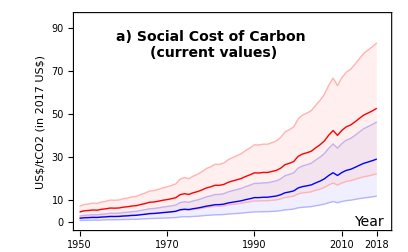

```mathematica
Figure1new=ListLinePlot[{SCCfixmeans[[2;;70,{2,5}]],SCCNSDRfixmeans[[2;;70,{2,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Blue,Thick} ,{Red,Thick}},IntervalMarkersStyle->{Lighter[Blue,0.7],Lighter[Red,0.7]}, PlotRange->{{1950,2020},{-2,95}},Frame->{True,True,False,False},Epilog->{Text[Style["a) Social Cost of Carbon \n(current values)",{FontFamily->"Helvetica",Bold,FontSize->14}],Offset[{0,0},Scaled[{0.44,0.85}]],{0,0}],Text[Style["Year",{FontFamily->"Helvetica",FontSize->14}],Offset[{0,0},Scaled[{0.93,0.04}]],{0,0.0}]},FrameTicks->{{{0,10,30,50,70,90},None},{{1950,1970,1990,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{None,"US$/tCO2 (in 2017 US$)",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotRangePadding->{0.0,0},ImageSize->17.8/2*72/2.54*{GoldenRatio,1}]
```

```mathematica
(*Figure1=ListLinePlot[{SCCfixmeans[[2;;70,{2,5}]],SCCoptmeans[[2;;70,{2,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Blue,Dashed,Thick},{Blue,Thick} },PlotLabel->"Social cost of carbon (current value)",Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","USD/tCO2 (2018)",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],ImageSize->600]*)
```

```mathematica
(*Export["figure1a_kappa_Drupp.png",Figure1, ImageResolution->400]*)
```

```mathematica
(*Figure2=ListLinePlot[{SCCpfixmeans[[2;;70,{2,5}]],SCCpoptmeans[[2;;70,{2,5}]],SCCpNSDRfixmeans[[2;;70,{2,5}]],SCCpNSDRoptmeans[[2;;70,{2,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Blue,Dashed,Thick},{Blue,Thick} ,{Red,Thick,Dashed},Red},IntervalMarkersStyle->{Lighter[Blue,0.7],Lighter[Blue,0.9],Lighter[Red,0.7],Lighter[Red,0.9]}, PlotRange->{{1950,2020},{-2,95}},Frame->{True,True,False,False},Epilog->{Text[Style["b) Social Cost of Carbon (present value in 2018)",{FontFamily->"Helvetica",FontSize->14}],Offset[{0,0},Scaled[{0.5,0.95}]],{0,0}],FrameTicks->{{{0,10,30,50,70,90},None},{{1950,1970,1990,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","US$/tCO2 (in 2017 US$)",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotRangePadding->{0.0,0},ImageSize->17.8/2*72/2.54*{GoldenRatio,1}]*)
```

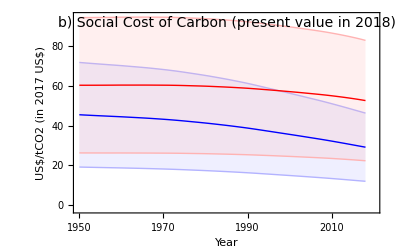

```mathematica
Figure2new=ListLinePlot[{SCCpfixmeans[[2;;70,{2,5}]],SCCpNSDRfixmeans[[2;;70,{2,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Blue,Thick} ,{Red,Thick}},IntervalMarkersStyle->{Lighter[Blue,0.7],Lighter[Red,0.7]}, PlotRange->{{1950,2020},{-2,95}},Frame->{True,True,False,False},Epilog->Text[Style["b) Social Cost of Carbon (present value in 2018)",{FontFamily->"Helvetica",FontSize->14}],Offset[{0,0},Scaled[{0.5,0.95}]],{0,0}],FrameTicks->{{{0,10,20,30,40,50,60,70,80,90},None},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","US$/tCO2 (in 2017 US$)",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotRangePadding->{0.0,0},ImageSize->17.8/2*72/2.54*{GoldenRatio,1}]
```

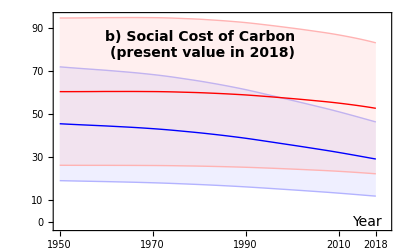

```mathematica
Figure2newb=ListLinePlot[{SCCpfixmeans[[2;;70,{2,5}]],SCCpNSDRfixmeans[[2;;70,{2,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Blue,Thick} ,{Red,Thick}},IntervalMarkersStyle->{Lighter[Blue,0.7],Lighter[Red,0.7]}, PlotRange->{{1950,2020},{-2,95}},Frame->{True,True,False,False},Epilog->{Text[Style["b) Social Cost of Carbon \n(present value in 2018)",{FontFamily->"Helvetica",Bold,FontSize->14}],Offset[{0,0},Scaled[{0.44,0.85}]],{0,0}],Text[Style["Year",{FontFamily->"Helvetica",FontSize->14}],Offset[{0,0},Scaled[{0.93,0.04}]],{0,0.0}]},FrameTicks->{{{0,10,30,50,70,90},None},{{1950,1970,1990,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotRangePadding->{0.0,0},ImageSize->17.8/2*72/2.54*{GoldenRatio,1}]
```

```mathematica
(*Figure1a=ListLinePlot[{SCCfixmeans[[2;;70,{2,6}]],SCCoptmeans[[2;;70,{2,6}]],SCCNSDRfixmeans[[2;;70,{2,6}]],SCCNSDRoptmeans[[2;;70,{2,6}]]},IntervalMarkers->"Bands",PlotStyle->{{Purple,Dashed,Thick},{Purple,Thick} ,{Orange,Thick,Dashed},Orange},IntervalMarkersStyle->{Lighter[Purple,0.7],Lighter[Purple,0.9],Lighter[Orange,0.7],Lighter[Orange,0.9]}, PlotRange->{{1950,2020},{-2,110}},Frame->{True,True,False,False},Epilog->Text[Style["a)",{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.05,0.9}]],{0,0}],FrameTicks->{{{0,10,20,30,40,50,60,70,80,90,100},None},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","USD/tCO2 (2017)",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],PlotRangePadding->{0.0,0},ImageSize->600];
Figure1b=ListLinePlot[{SCCfixmeans[[2;;70,{2,7}]],SCCoptmeans[[2;;70,{2,7}]],SCCNSDRfixmeans[[2;;70,{2,7}]],SCCNSDRoptmeans[[2;;70,{2,7}]]},IntervalMarkers->"Bands",PlotStyle->{{Purple,Dashed,Thick},{Purple,Thick} ,{Orange,Thick,Dashed},Orange},IntervalMarkersStyle->{Lighter[Purple,0.7],Lighter[Purple,0.9],Lighter[Orange,0.7],Lighter[Orange,0.9]}, PlotRange->{{1950,2020},{-2,110}},Frame->{True,True,False,False},Epilog->Text[Style["b)",{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.05,0.9}]],{0,0}],FrameTicks->{{{0,10,20,30,40,50,60,70,80,90,100},None},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","USD/tCO2 (2017)",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],PlotRangePadding->{0.0,0},ImageSize->600];
Figure1c=ListLinePlot[{SCCfixmeans[[2;;70,{2,8}]],SCCoptmeans[[2;;70,{2,8}]],SCCNSDRfixmeans[[2;;70,{2,8}]],SCCNSDRoptmeans[[2;;70,{2,8}]]},IntervalMarkers->"Bands",PlotStyle->{{Purple,Dashed,Thick},{Purple,Thick} ,{Orange,Thick,Dashed},Orange},IntervalMarkersStyle->{Lighter[Purple,0.7],Lighter[Purple,0.9],Lighter[Orange,0.7],Lighter[Orange,0.9]}, PlotRange->{{1950,2020},{-2,110}},Frame->{True,True,False,False},Epilog->Text[Style["c) ",{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.05,0.9}]],{0,0}],FrameTicks->{{{0,10,20,30,40,50,60,70,80,90,100},None},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","USD/tCO2 (2017)",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],PlotRangePadding->{0.0,0},ImageSize->600];Figure7=ListLinePlot[{SCCfixmeans[[2;;70,{2,6}]],SCCoptmeans[[2;;70,{2,6}]],SCCNSDRfixmeans[[2;;70,{2,6}]],SCCNSDRoptmeans[[2;;70,{2,6}]]},IntervalMarkers->"Bands",PlotStyle->{{Purple,Thick,Dashed},Purple,{Orange,Thick,Dashed},Orange},PlotLabel->"Nordhau Impact function SCC fix versus opt (uncertainty)",Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","USD/tCO2",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],ImageSize->600]Figure8=ListLinePlot[{SCCfixmeans[[2;;59,{2,7}]],SCCoptmeans[[2;;59,{2,7}]]},IntervalMarkers->"Bands",PlotStyle->{Red,{Red,Thick,Dashed}},PlotLabel->"Howard&Sterner Impact func SCC fix versus opt (uncertainty)",Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","USD/tCO2",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],ImageSize->600]Figure9=ListLinePlot[{SCCfixmeans[[2;;59,{2,8}]],SCCoptmeans[[2;;59,{2,8}]]},IntervalMarkers->"Bands",PlotStyle->{Green,{Green,Thick,Dashed}},PlotLabel->"Weitzman Impact func SCC fix versus opt (uncertainty)",Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","USD/tCO2",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],ImageSize->600]*)
```

```mathematica
(*Figure3=ListLinePlot[{Efixmeans[[2;;70,{2,3}]],Eoptmeans[[2;;70,{2,5}]],ENSDRoptmeans[[2;;70,{2,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Black,Thick},{Blue,Thick} ,{Red,Thick}},IntervalMarkersStyle->{Gray,Lighter[Blue,0.7],Lighter[Red,0.7]}, PlotRange->{{1950,2020},{1,10}},Frame->{True,True,False,False},Epilog->Text[Style["c) Energy&Industrial CO_2 Emissions",{FontFamily->"Helvetica",FontSize->14}],Offset[{0,0},Scaled[{0.35,0.95}]],{0,0}],FrameTicks->{{{2,4,6,8},None},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","Gt C",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotRangePadding->{0,0},ImageSize->17.8/2*72/2.54*{GoldenRatio,1}]*)
```

```mathematica
(*Figure11=ListLinePlot[{Efixmeans[[2;;70,{2,3}]],Eoptmeans[[2;;70,{2,6}]],Eoptmeans[[2;;70,{2,7}]],Eoptmeans[[2;;70,{2,8}]],ENSDRoptmeans[[2;;70,{2,6}]],ENSDRoptmeans[[2;;70,{2,7}]],ENSDRoptmeans[[2;;70,{2,8}]]},IntervalMarkers->"None",PlotStyle->{Black,Blue,Red,Green,{Blue,Dashed},{Red,Dashed},{Green,Dashed}},PlotLabel->"Emissions observed versus opt",Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","GtC",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],ImageSize->600]*)
```

```mathematica
(*Figure12=ListLinePlot[{obsdata[[2;;70,{1,9}]],Catmoptmeans[[2;;70,{2,5}]],CatmNSDRoptmeans[[2;;70,{2,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Black,Thick},{Red,Thick},{Orange,Thick}},PlotLabel->"Catm observed versus optimal",Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","ppm CO2",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],ImageSize->600]*)
```

```mathematica
(*Figure4=ListLinePlot[{obsdata[[2;;70,{1,8}]],Tfixmeans[[2;;70,{2,5}]],Toptmeans[[2;;70,{2,5}]],TNSDRoptmeans[[2;;70,{2,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Black,Thick},{Black,Dashed,Thick},{Blue,Thick} ,{Red,Thick}},IntervalMarkersStyle->{Gray,Lighter[Blue,0.7],Lighter[Red,0.7]}, PlotRange->{{1950,2020},{0,1.3}},Frame->{True,True,False,False},Epilog->Text[Style["d)Temperature Increase",{FontFamily->"Helvetica",FontSize->14}],Offset[{0,0},Scaled[{0.25,0.95}]],{0,0}],FrameTicks->{{{0.2,0.4,0.6,0.8,1.0, 1.2},None},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","°C relative to 1850-1900",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotRangePadding->{0.0,0},ImageSize->17.8/2*72/2.54*{GoldenRatio,1}];*)
```

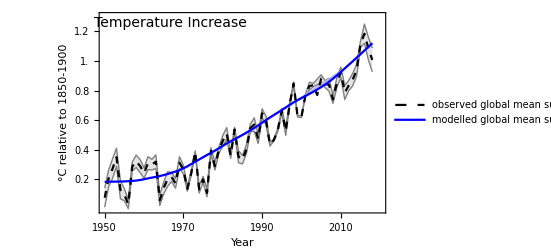

```mathematica
SIFtemp=Legended[ListLinePlot[{obsdata[[2;;70,{1,8}]],Tfixmeans[[2;;70,{2,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Black,Dashed,Thick},{Blue,Thick}},IntervalMarkersStyle->{Gray,Lighter[Blue,0.7]}, PlotRange->{{1950,2020},{0,1.3}},Frame->{True,True,False,False},Epilog->Text[Style["Temperature Increase",{FontFamily->"Helvetica",FontSize->14}],Offset[{0,0},Scaled[{0.25,0.95}]],{0,0}],FrameTicks->{{{0.2,0.4,0.6,0.8,1.0, 1.2},None},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"Year","°C relative to 1850-1900",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotRangePadding->{0.0,0},ImageSize->17.8/2*72/2.54*{GoldenRatio,1}],Placed[LineLegend[{{Black,Dashed},Blue},{Style["observed global mean surface air temperature",FontFamily->"Helvetica",FontSize->14],Style["modelled global mean surface air temperature",FontFamily->"Helvetica",FontSize->14]},LegendLayout->{"Row",3}],Below]]
```

```mathematica
Export["SIFtemp.eps",SIFtemp]
```

SIFtemp.eps

```mathematica
(*Fig1L=Legended[Grid[{{Figure1,Figure2},{Figure3,Figure4}},Frame->False],Placed[LineLegend[{{Blue,AbsoluteThickness[3]},{Blue,Dashed,AbsoluteThickness[3]},{Red,AbsoluteThickness[3]},{Red,Dashed,AbsoluteThickness[3]},{Black,AbsoluteThickness[3]},{Black,Dashed,AbsoluteThickness[3]},Black},{Style["SCC optimal abatement (calibrated: η=1.45, δ=1.95%)",FontFamily->"Helvetica",FontSize->14],Style["SCC observed abatement (calibrated: η=1.45, δ=1.95%)",FontFamily->"Helvetica",FontSize->14],Style["SCC optimal abatement (Drupp et al. 2018: η=1.35, δ=1.1%)",FontFamily->"Helvetica",FontSize->14],Style["SCC observed abatement (Drupp et al. 2018: η=1.35, δ=1.1%)",FontFamily->"Helvetica",FontSize->14],Style["observed emissions and temperature increase",FontFamily->"Helvetica",FontSize->14],Style["model-based temperature increase for observed emissions",FontFamily->"Helvetica",FontSize->14]},LegendLayout->{"Row",3}],Below]]*)
```

```mathematica
results2=Table["",{i,28},{j,19}];
results2[[1,4;;]]={"2018","2018","2019","2019","2019","2019","2019","2019","2100","2100","2100","2100","2100","2100","2100","2100"};
results2[[2,4;;]]={"SCC","","Catm","","Temp","","Capital","","SCC","","Catm","","Temp","","Capital",""};
results2[[3,4;;]]={"USD/tCO2","USD/tCO2","ppm","ppm","°C","°C","10^12 USD","10^12 USD","USD/tCO2","USD/tCO2","ppm","ppm","°C","°C","10^12 USD","10^12 USD"};
results2[[4,4;;]]={"Mean","SD","Mean","SD","Mean","SD","Mean","SD","Mean","SD","Mean","SD","Mean","SD","Mean","SD"};
results2[[5,1]]="eta/rho=RMQ";
results2[[17,1]]="eta/rho=N";
results2[[{5,9,13,17,21,25},2]]={"Nordhaus","Sterner","Weitzman","Nordhaus","Sterner","Weitzman"};
results2[[5;;,3]]={"fix","opt","Iopt","optopt","fix","opt","Iopt","optopt","fix","opt","Iopt","optopt","fix","opt","Iopt","optopt","fix","opt","Iopt","optopt","fix","opt","Iopt","optopt"};
```

```mathematica
results2//MatrixForm
```

( |  |  | 2018 | 2018 | 2019 | 2019 | 2019 | 2019 | 2019 | 2019 | 2100 | 2100 | 2100 | 2100 | 2100 | 2100 | 2100 | 2100
 |  |  | SCC |  | Catm |  | Temp |  | Capital |  | SCC |  | Catm |  | Temp |  | Capital | 
 |  |  | USD/tCO2 | USD/tCO2 | ppm | ppm | °C | °C | 10^12 USD | 10^12 USD | USD/tCO2 | USD/tCO2 | ppm | ppm | °C | °C | 10^12 USD | 10^12 USD
 |  |  | Mean | SD | Mean | SD | Mean | SD | Mean | SD | Mean | SD | Mean | SD | Mean | SD | Mean | SD
eta/rho=RMQ | Nordhaus | fix | 15.8795 | 3.13214 | 408.664 | 0. | 1.14404 | 0. | 562.021 | 0. | 131.898 | 44.4314 | 638.844 | 72.236 | 3.01768 | 0.392945 | 3141.3 | 896.497
 |  | opt | 15.6897 | 3.07545 | 403.122 | 1.0664 | 1.10632 | 0.005816 | 562.021 | 0. | 131.404 | 44.2781 | 633.763 | 71.4473 | 2.99024 | 0.391826 | 3143.16 | 896.943
 |  | Iopt | 16.6823 | 2.72511 | 408.692 | 0.525066 | 1.14324 | 0.002445 | 568.998 | 24.7007 | 131.869 | 44.3892 | 638.932 | 72.7693 | 3.01769 | 0.394725 | 3141.72 | 896.093
 |  | optopt | 16.4826 | 2.68089 | 403.142 | 0.567843 | 1.10577 | 0.003465 | 569.059 | 24.6869 | 131.381 | 44.2315 | 633.873 | 71.9928 | 2.99038 | 0.393648 | 3143.58 | 896.539
 | Sterner | fix | 50.4114 | 10.8425 | 408.664 | 0. | 1.14404 | 0. | 562.021 | 0. | 369.925 | 100.004 | 501.628 | 28.8863 | 2.41042 | 0.228952 | 3037.84 | 861.598
 |  | opt | 48.6305 | 10.2307 | 395.015 | 1.91342 | 1.05993 | 0.010618 | 562.021 | 0. | 363.391 | 97.9325 | 493.089 | 27.8394 | 2.35044 | 0.226726 | 3049.47 | 865.078
 |  | Iopt | 52.7517 | 9.45882 | 408.294 | 0.464429 | 1.14088 | 0.002082 | 562.619 | 23.7338 | 369.589 | 99.7538 | 501.287 | 29.0676 | 2.40783 | 0.229723 | 3038.5 | 861.469
 |  | optopt | 51.04 | 9.03024 | 394.727 | 1.43187 | 1.05783 | 0.008368 | 562.879 | 23.7037 | 363.114 | 97.694 | 492.837 | 28.0426 | 2.34845 | 0.227579 | 3050.02 | 864.932
 | Weitzman | fix | 21.2149 | 6.74783 | 408.664 | 0. | 1.14404 | 0. | 562.021 | 0. | 244.502 | 74.736 | 571.142 | 38.2677 | 2.74752 | 0.271013 | 3127.08 | 893.036
 |  | opt | 20.6473 | 6.4203 | 401.826 | 1.77412 | 1.09924 | 0.00974 | 562.021 | 0. | 239.995 | 73.8005 | 567.492 | 38.2563 | 2.72255 | 0.271332 | 3130.16 | 893.759
 |  | Iopt | 22.2392 | 6.31807 | 408.629 | 0.489574 | 1.14289 | 0.002242 | 567.626 | 23.9362 | 244.364 | 74.599 | 571.089 | 38.4295 | 2.74691 | 0.271613 | 3127.5 | 892.696
 |  | optopt | 21.6579 | 6.02418 | 401.785 | 1.33345 | 1.09841 | 0.007669 | 567.729 | 23.936 | 239.88 | 73.6641 | 567.452 | 38.42 | 2.72206 | 0.271941 | 3130.57 | 893.418
eta/rho=N | Nordhaus | fix | 29.7257 | 6.88274 | 408.664 | 0. | 1.14404 | 0. | 562.021 | 0. | 213.079 | 65.639 | 594.589 | 53.6766 | 2.84276 | 0.329698 | 3927.94 | 1103.04
 |  | opt | 29.1291 | 6.67665 | 398.447 | 2.01972 | 1.07894 | 0.011501 | 562.021 | 0. | 211.064 | 64.9192 | 586.428 | 52.3715 | 2.79503 | 0.326919 | 3931.87 | 1103.82
 |  | Iopt | 32.0125 | 6.11208 | 416.299 | 0.654621 | 1.18883 | 0.003056 | 696.387 | 32.254 | 215.13 | 66.2631 | 602.335 | 54.0646 | 2.8869 | 0.327633 | 3932.64 | 1101.18
 |  | optopt | 31.4054 | 5.98737 | 404.984 | 1.55972 | 1.11877 | 0.009211 | 696.524 | 32.2068 | 213.094 | 65.3949 | 593.381 | 52.6911 | 2.83526 | 0.324833 | 3936.97 | 1102.05
 | Sterner | fix | 89.2539 | 21.1091 | 408.664 | 0. | 1.14404 | 0. | 562.021 | 0. | 510.48 | 116.857 | 443.982 | 18.6546 | 2.09053 | 0.159377 | 3817.32 | 1063.09
 |  | opt | 84.0353 | 19.0994 | 387.594 | 3.01344 | 1.01521 | 0.017582 | 562.021 | 0. | 490.787 | 110.375 | 433.64 | 17.7523 | 2.00694 | 0.156248 | 3836.83 | 1066.09
 |  | Iopt | 95.4251 | 18.3149 | 415.629 | 0.56542 | 1.18485 | 0.002485 | 686.101 | 31.7621 | 517.175 | 118.979 | 447.02 | 18.4129 | 2.11541 | 0.155695 | 3818.44 | 1061.03
 |  | optopt | 90.4079 | 16.9837 | 392.569 | 2.61646 | 1.04724 | 0.015589 | 686.564 | 31.5841 | 496.003 | 111.844 | 435.753 | 17.5593 | 2.02522 | 0.152817 | 3839.59 | 1064.2
 | Weitzman | fix | 38.9433 | 12.8738 | 408.664 | 0. | 1.14404 | 0. | 562.021 | 0. | 305.813 | 78.0174 | 536.887 | 26.9869 | 2.58978 | 0.222409 | 3915.11 | 1096.58
 |  | opt | 37.2706 | 11.9346 | 396.709 | 2.84569 | 1.06905 | 0.016299 | 562.021 | 0. | 297.351 | 76.8762 | 531.405 | 27.1125 | 2.54902 | 0.223651 | 3921.18 | 1097.96
 |  | Iopt | 42.4743 | 12.2119 | 416.226 | 0.602437 | 1.18845 | 0.002746 | 694.294 | 31.4457 | 312.44 | 78.475 | 540.913 | 26.0551 | 2.61926 | 0.215499 | 3918.63 | 1094.2
 |  | optopt | 40.6109 | 11.3561 | 402.878 | 2.53359 | 1.10707 | 0.014716 | 694.48 | 31.3991 | 303.039 | 77.252 | 534.969 | 26.2312 | 2.57531 | 0.217107 | 3925.47 | 1095.79)

```mathematica
results2[[5,4;;5]]=Nfix[[70,{3,4}]];
results2[[5,6;;11]]=Nfix[[71,{11,12,13,14,17,18}]];
results2[[5,12;;]]=Nfix[[152,{3,4,11,12,13,14,17,18}]];
results2[[6,4;;5]]=Nopt[[70,{3,4}]];
results2[[6,6;;11]]=Nopt[[71,{11,12,13,14,17,18}]];
results2[[6,12;;]]=Nopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[7,4;;5]]=NIopt[[70,{3,4}]];
results2[[7,6;;11]]=NIopt[[71,{11,12,13,14,17,18}]];
results2[[7,12;;]]=NIopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[8,4;;5]]=Noptopt[[70,{3,4}]];
results2[[8,6;;11]]=Noptopt[[71,{11,12,13,14,17,18}]];
results2[[8,12;;]]=Noptopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[9,4;;5]]=HSfix[[70,{3,4}]];
results2[[9,6;;11]]=HSfix[[71,{11,12,13,14,17,18}]];
results2[[9,12;;]]=HSfix[[152,{3,4,11,12,13,14,17,18}]];
results2[[10,4;;5]]=HSopt[[70,{3,4}]];
results2[[10,6;;11]]=HSopt[[71,{11,12,13,14,17,18}]];
results2[[10,12;;]]=HSopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[11,4;;5]]=HSIopt[[70,{3,4}]];
results2[[11,6;;11]]=HSIopt[[71,{11,12,13,14,17,18}]];
results2[[11,12;;]]=HSIopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[12,4;;5]]=HSoptopt[[70,{3,4}]];
results2[[12,6;;11]]=HSoptopt[[71,{11,12,13,14,17,18}]];
results2[[12,12;;]]=HSoptopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[13,4;;5]]=Wfix[[70,{3,4}]];
results2[[13,6;;11]]=Wfix[[71,{11,12,13,14,17,18}]];
results2[[13,12;;]]=Wfix[[152,{3,4,11,12,13,14,17,18}]];
results2[[14,4;;5]]=Wopt[[70,{3,4}]];
results2[[14,6;;11]]=Wopt[[71,{11,12,13,14,17,18}]];
results2[[14,12;;]]=Wopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[15,4;;5]]=WIopt[[70,{3,4}]];
results2[[15,6;;11]]=WIopt[[71,{11,12,13,14,17,18}]];
results2[[15,12;;]]=WIopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[16,4;;5]]=Woptopt[[70,{3,4}]];
results2[[16,6;;11]]=Woptopt[[71,{11,12,13,14,17,18}]];
results2[[16,12;;]]=Woptopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[17,4;;5]]=NNSDRfix[[70,{3,4}]];
results2[[17,6;;11]]=NNSDRfix[[71,{11,12,13,14,17,18}]];
results2[[17,12;;]]=NNSDRfix[[152,{3,4,11,12,13,14,17,18}]];
results2[[18,4;;5]]=NNSDRopt[[70,{3,4}]];
results2[[18,6;;11]]=NNSDRopt[[71,{11,12,13,14,17,18}]];
results2[[18,12;;]]=NNSDRopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[19,4;;5]]=NNSDRIopt[[70,{3,4}]];
results2[[19,6;;11]]=NNSDRIopt[[71,{11,12,13,14,17,18}]];
results2[[19,12;;]]=NNSDRIopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[20,4;;5]]=NNSDRoptopt[[70,{3,4}]];
results2[[20,6;;11]]=NNSDRoptopt[[71,{11,12,13,14,17,18}]];
results2[[20,12;;]]=NNSDRoptopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[21,4;;5]]=HSNSDRfix[[70,{3,4}]];
results2[[21,6;;11]]=HSNSDRfix[[71,{11,12,13,14,17,18}]];
results2[[21,12;;]]=HSNSDRfix[[152,{3,4,11,12,13,14,17,18}]];
results2[[22,4;;5]]=HSNSDRopt[[70,{3,4}]];
results2[[22,6;;11]]=HSNSDRopt[[71,{11,12,13,14,17,18}]];
results2[[22,12;;]]=HSNSDRopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[23,4;;5]]=HSNSDRIopt[[70,{3,4}]];
results2[[23,6;;11]]=HSNSDRIopt[[71,{11,12,13,14,17,18}]];
results2[[23,12;;]]=HSNSDRIopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[24,4;;5]]=HSNSDRoptopt[[70,{3,4}]];
results2[[24,6;;11]]=HSNSDRoptopt[[71,{11,12,13,14,17,18}]];
results2[[24,12;;]]=HSNSDRoptopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[25,4;;5]]=WNSDRfix[[70,{3,4}]];
results2[[25,6;;11]]=WNSDRfix[[71,{11,12,13,14,17,18}]];
results2[[25,12;;]]=WNSDRfix[[152,{3,4,11,12,13,14,17,18}]];
results2[[26,4;;5]]=WNSDRopt[[70,{3,4}]];
results2[[26,6;;11]]=WNSDRopt[[71,{11,12,13,14,17,18}]];
results2[[26,12;;]]=WNSDRopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[27,4;;5]]=WNSDRIopt[[70,{3,4}]];
results2[[27,6;;11]]=WNSDRIopt[[71,{11,12,13,14,17,18}]];
results2[[27,12;;]]=WNSDRIopt[[152,{3,4,11,12,13,14,17,18}]];
results2[[28,4;;5]]=WNSDRoptopt[[70,{3,4}]];
results2[[28,6;;11]]=WNSDRoptopt[[71,{11,12,13,14,17,18}]];
results2[[28,12;;]]=WNSDRoptopt[[152,{3,4,11,12,13,14,17,18}]];
```

```mathematica
Export["results2.csv",results2]
```

results2.csv

```mathematica
(*results3=Table["",{i,10},{j,10}];
results3[[1,3;;]]={"I fix, mu fix","","I opt, mu fix","","I fix, mu opt","","I opt, mu opt",""};
results3[[2,3;;]]={"mean","std","mean","std","mean","std","mean","std"};
results3[[3,6]]="eta/rho=RMQ";
results3[[7,6]]="eta/rho=Drupp";
results3[[3,1]]="K2019";
results3[[7,1]]="K2019";
results3[[{4,5,6,8,9,10},2]]={"Nordhaus","Sterner","Weitzman","Nordhaus","Sterner","Weitzman"};
results3[[4,3;;4]]=Nfix[[71,17;;18]];
results3[[4,5;;6]]=NIopt[[71,17;;18]];
results3[[4,7;;8]]=Nopt[[71,17;;18]];
results3[[4,9;;10]]=Noptopt[[71,17;;18]];
results3[[5,3;;4]]=HSfix[[71,17;;18]];
results3[[5,5;;6]]=HSIopt[[71,17;;18]];
results3[[5,7;;8]]=HSopt[[71,17;;18]];
results3[[5,9;;10]]=HSoptopt[[71,17;;18]];
results3[[6,3;;4]]=Wfix[[71,17;;18]];
results3[[6,5;;6]]=WIopt[[71,17;;18]];
results3[[6,7;;8]]=Wopt[[71,17;;18]];
results3[[6,9;;10]]=Woptopt[[71,17;;18]];
results3[[8,3;;4]]=NNSDRfix[[71,17;;18]];
results3[[8,5;;6]]=NNSDRIopt[[71,17;;18]];
results3[[8,7;;8]]=NNSDRopt[[71,17;;18]];
results3[[8,9;;10]]=NNSDRoptopt[[71,17;;18]];
results3[[9,3;;4]]=HSNSDRfix[[71,17;;18]];
results3[[9,5;;6]]=HSNSDRIopt[[71,17;;18]];
results3[[9,7;;8]]=HSNSDRopt[[71,17;;18]];
results3[[9,9;;10]]=HSNSDRoptopt[[71,17;;18]];
results3[[10,3;;4]]=WNSDRfix[[71,17;;18]];
results3[[10,5;;6]]=WNSDRIopt[[71,17;;18]];
results3[[10,7;;8]]=WNSDRopt[[71,17;;18]];
results3[[10,9;;10]]=WNSDRoptopt[[71,17;;18]];
results3//MatrixForm*)
```

( |  | I fix, mu fix |  | I opt, mu fix |  | I fix, mu opt |  | I opt, mu opt | 
 |  | mean | std | mean | std | mean | std | mean | std
K2019 |  |  |  |  | eta/rho=RMQ |  |  |  | 
 | Nordhaus | 562.021 | 0. | 568.998 | 24.7007 | 562.021 | 0. | 569.059 | 24.6869
 | Sterner | 562.021 | 0. | 562.619 | 23.7338 | 562.021 | 0. | 562.879 | 23.7037
 | Weitzman | 562.021 | 0. | 567.626 | 23.9362 | 562.021 | 0. | 567.729 | 23.936
K2019 |  |  |  |  | eta/rho=Drupp |  |  |  | 
 | Nordhaus | 562.021 | 0. | 696.387 | 32.254 | 562.021 | 0. | 696.524 | 32.2068
 | Sterner | 562.021 | 0. | 686.101 | 31.7621 | 562.021 | 0. | 686.564 | 31.5841
 | Weitzman | 562.021 | 0. | 694.294 | 31.4457 | 562.021 | 0. | 694.48 | 31.3991)

```mathematica
SetDirectory["C:\\Users\\Rickels\\Dropbox\\Historic_DICE_Dropbox\\IW_Calculations\\Global"];
```

```mathematica
iwglob=Import["IW_output_global.csv"];
```

```mathematica
SetDirectory["C:\\Users\\Rickels\\Dropbox\\Historic_DICE_Dropbox\\IW_Calculations\\Country_Results"];
```

```mathematica
iwraw=Import["IW_input.csv"];
```

```mathematica
cumsharedata=Table[0,{i,20},{j,3}];
cumsharedata[[;;,1]]=iwraw[[3;;22,3]];
Do[cumsharedata[[i,2]]=Around[iwraw[[i+2,7]],iwraw[[i+77,7]]],{i,1,20}]
cumsharedata[[{3,10},2]]="";
```

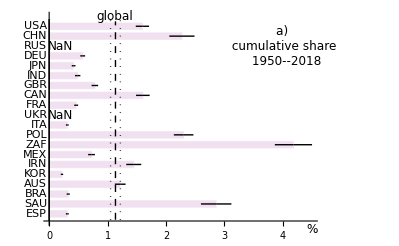

```mathematica
Fig2a=Show[BarChart[Reverse[cumsharedata[[;;,2]]],IntervalMarkers->"Fences",BarOrigin->Left,BarSpacing->0.5,ChartStyle->LightPurple,ChartLabels->Reverse[cumsharedata[[;;,1]]],Epilog->{Text[Style["global",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.26,0.98}]],{0,0}],Text[Style["%",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.98,-0.02}]],{0,0}],Text[Style["a) \n cumulative share \n 1950--2018",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.88,0.84}]],{0,0}],Text[Style["NaN",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.06,0.84}]],{0,0}],Text[Style["NaN",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.06,0.515}]],{0,0}]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->12,Black],
ImageSize->8.7*72/2.54*{GoldenRatio,1}],Graphics[{{Black,Dotted,Thin,Line[{{1.135+0.083810015848264,0.4},{1.135+0.083810015848264,21}}]},{Black,Dotted,Thin,Line[{{1.135-0.083810015848264,0.4},{1.135-0.083810015848264,21}}]},{Black,Dashed,Thick,Line[{{1.135,0.4},{1.135,20.5}}]}}]]
```

```mathematica
sharedata=Table[0,{i,70},{j,22}];
sharedata[[2;;,1]]=iwraw[[2,7;;]];
sharedata[[1,2;;21]]=iwraw[[3;;22,3]];
sharedata[[1,22]]="global";
Do[Do[sharedata[[i+2,2+j]]=Around[iwraw[[3+j,i+7]],iwraw[[78+j,i+7]]],{i,0,68}],{j,0,19}]
Do[sharedata[[i+2,22]]=Around[iwglob[[1,i+1]],iwglob[[2,i+1]]],{i,0,68}]
```

```mathematica
sharehdata=Table[0,{i,70},{j,22}];
sharehdata[[2;;,1]]=iwraw[[2,7;;]];
sharehdata[[1,2;;21]]=iwraw[[3;;22,3]];
sharehdata[[1,22]]="global";
Do[Do[sharehdata[[i+2,2+j]]=iwraw[[3+j,i+7]],{i,0,68}],{j,0,19}]
Do[sharehdata[[i+2,22]]=iwglob[[1,i+1]],{i,0,68}]
```

```mathematica
sharehfdata=sharedata;
sharehfdata[[2;;,2;;]]=Reverse[sharehdata[[2;;,2;;]]];
```

```mathematica
Fig2b=ListLinePlot[{sharedata[[2;;,{1,22}]],sharedata[[2;;,{1,2}]],sharedata[[2;;,{1,3}]],sharedata[[2;;,{1,5}]],sharedata[[2;;,{1,6}]],sharedata[[2;;,{1,7}]]},PlotStyle->{{Black,AbsoluteThickness[3]}, Blue, Red,Orange,Purple,Darker[Green]},IntervalMarkers->"None",PlotRange->{{1950,2022},{0,4.5}},Frame->{True,True,False,False},FrameTicks->{{{1,2,3,4,5,6},{1,2,3,4,5,6}},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Automatic},Epilog->{Text[Style["start year for accounting",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.82,0.04}]],{0,0}],Text[Style["%",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.02,0.95}]],{0,0}],Text[Style["b) \n cumulative share \n start year--2018",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.24,0.82}]],{0,0}],Text[Style["USA",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.05,0.405}]],{0,0}],Text[Style["China",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.06,0.54}]],{0,0}],
Text[Style["India",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.9,0.28}]],{0,0}],
Text[Style["Japan",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.58,0.32}]],{0,0}],
Text[Style["Germany",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.07,0.19}]],{0,0}],
Text[Style["global",{FontFamily->"Helvetica",FontSize->12,Bold}],Offset[{0,0},Scaled[{0.06,0.30}]],{0,0}]},ImageSize->8.7*72/2.54*{GoldenRatio,1}];
```

```mathematica
(*Fig2bb=ListLinePlot[{Reverse[sharehdata[[2;;,{22,1}]]],Reverse[sharehdata[[2;;,{2,1}]]],Reverse[sharehdata[[2;;,{3,1}]]],Reverse[sharehdata[[2;;,{5,1}]]],Reverse[sharehdata[[2;;,{6,1}]]],Reverse[sharehdata[[2;;,{7,1}]]]},PlotStyle->{{Black,AbsoluteThickness[3]}, Blue, Red,Orange,Purple,Darker[Green]},IntervalMarkers->"None",PlotRange->{{0,4.5},{1950,2018}},Frame->{True,True,False,False},FrameTicks->{{{1950,1960,1970,1980,1990,2000,2010,2018},{1,2,3,4,5,6}},{{1,2,3,4,5,6},None}},FrameStyle->{Black,Black,Automatic,Automatic},ImageSize->8.7*72/2.54*{GoldenRatio,1}];*)
```

```mathematica
(*check=Table[0,{i,69},{j,2}];
check[[;;,1]]=sharehfdata[[2;;,1]];
check[[;;,2]]=Reverse[sharehfdata[[2;;,1]]];*)
```

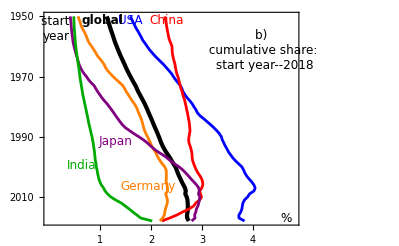

```mathematica
Fig2bc=ListLinePlot[{sharehfdata[[2;;,{22,1}]],sharehfdata[[2;;,{2,1}]],sharehfdata[[2;;,{3,1}]],sharehfdata[[2;;,{5,1}]],sharehfdata[[2;;,{6,1}]],sharehfdata[[2;;,{7,1}]]},PlotStyle->{{Black,AbsoluteThickness[3]}, {Blue,AbsoluteThickness[2]}, {Red,AbsoluteThickness[2]},{Orange,AbsoluteThickness[2]},{Purple,AbsoluteThickness[2]},{Darker[Green],AbsoluteThickness[2]}},IntervalMarkers->"None",PlotRange->{{0,4.8},{1950,2018}},Frame->{True,True,False,False},FrameTicks->{{{{2018,1950},{2008,1960},{1998,1970},{1988,1980},{1978,1990},{1968,2000},{1958,2010},{1950,2018}},None},{{{0.2,""},{0.4,""},{0.6,""},{0.8,""},{1,1},{1.2,""},{1.4,""},{1.6,""},{1.8,""},{2,2},{2.2,""},{2.4,""},{2.6,""},{2.8,""},{3,3},{3.2,""},{3.4,""},{3.6,""},{3.8,""},{4,4},{4.2,""},{4.4,""}},None}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->12,Black],PlotRangePadding->{{0,0},{1,6}},FrameStyle->{Black,Black,Automatic,Automatic},Epilog->{Text[Style["start \nyear",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.05,0.92}]],{0,0}],Text[Style["%",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.95,0.03}]],{0,0}],Text[Style["b) \n cumulative share: \n start year--2018",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.86,0.82}]],{0,0}],Text[Style["USA",{FontFamily->"Helvetica",FontSize->12},Blue],Offset[{0,0},Scaled[{0.34,0.96}]],{0,0}],Text[Style["China",{FontFamily->"Helvetica",FontSize->12},Red],Offset[{0,0},Scaled[{0.48,0.96}]],{0,0}],
Text[Style["India",{FontFamily->"Helvetica",FontSize->12},Darker[Green]],Offset[{0,0},Scaled[{0.15,0.28}]],{0,0}],
Text[Style["Japan",{FontFamily->"Helvetica",FontSize->12,Purple}],Offset[{0,0},Scaled[{0.28,0.395}]],{0,0}],
Text[Style["Germany",{FontFamily->"Helvetica",FontSize->12,Orange}],Offset[{0,0},Scaled[{0.41,0.18}]],{0,0}],
Text[Style["global",{FontFamily->"Helvetica",FontSize->12,Bold}],Offset[{0,0},Scaled[{0.23,0.96}]],{0,0}]},ImageSize->8.7*72/2.54*{GoldenRatio,1}]
```

```mathematica
(*Fig2bd=ListLinePlot[{sharehfdata[[2;;,{22,1}]],sharehfdata[[2;;,{2,1}]],sharehfdata[[2;;,{3,1}]],sharehfdata[[2;;,{5,1}]],sharehfdata[[2;;,{6,1}]],sharehfdata[[2;;,{7,1}]]},PlotStyle->{{Black,AbsoluteThickness[3]}, Blue, Red,Orange,Purple,Darker[Green]},IntervalMarkers->"None",PlotRange->{{0,4.5},{1950,2018}},Frame->{True,True,False,False},FrameTicks->{{{{2018,"1950-2018"},{2008,"1960-2018"},{1998,"1970-2018"},{1988,"1980-2018"},{1978,"1990-2018"},{1968,"2000-2018"},{1958,"2010-2018"},{1950,2018}},{1,2,3,4,5,6}},{{1,2,3,4,5,6},None}},PlotRangePadding->{{0,0.1},{1,0.1}},FrameStyle->{Black,Black,Automatic,Automatic},ImageSize->8.7*72/2.54*{GoldenRatio,1}]*)
```

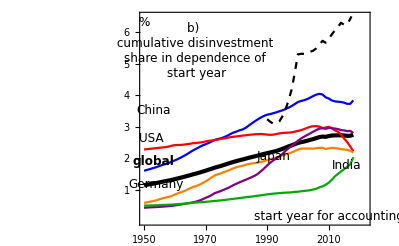

```mathematica
(*Fig2balt=ListLinePlot[{sharedata[[2;;,{1,22}]],sharedata[[2;;,{1,2}]],sharedata[[2;;,{1,3}]],sharedata[[2;;,{1,5}]],sharedata[[2;;,{1,6}]],sharedata[[2;;,{1,7}]],sharedata[[2;;,{1,4}]]},PlotStyle->{{Black,AbsoluteThickness[3]}, Blue, Red,Orange,Purple,Darker[Green],{Dashed,Black}},IntervalMarkers->"None",PlotRange->{{1950,2022},{0,6.5}},Frame->{True,True,False,False},FrameTicks->{{{1,2,3,4,5,6},{1,2,3,4,5,6}},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Automatic},Epilog->{Text[Style["start year for accounting",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.82,0.04}]],{0,0}],Text[Style["%",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.02,0.95}]],{0,0}],Text[Style["b) \n cumulative disinvestment \n share in dependence of \n start year",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.24,0.82}]],{0,0}],Text[Style["USA",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.05,0.405}]],{0,0}],Text[Style["China",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.06,0.54}]],{0,0}],
Text[Style["India",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.9,0.28}]],{0,0}],
Text[Style["Japan",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.58,0.32}]],{0,0}],
Text[Style["Germany",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.07,0.19}]],{0,0}],
Text[Style["global",{FontFamily->"Helvetica",FontSize->12,Bold}],Offset[{0,0},Scaled[{0.06,0.30}]],{0,0}]},ImageSize->8.7*72/2.54*{GoldenRatio,1}]*)
```

```mathematica
percapdata=Table[0,{i,70},{j,22}];
percapdata[[2;;,1]]=iwraw[[2,7;;]];
percapdata[[1,2;;21]]=iwraw[[3;;22,3]];
percapdata[[1,22]]="global";
Do[Do[percapdata[[i+2,2+j]]=Around[iwraw[[53+j,i+7]],iwraw[[128+j,i+7]]],{i,0,68}],{j,0,19}]
Do[percapdata[[i+2,22]]=Around[iwglob[[5,i+1]],iwglob[[6,i+1]]],{i,0,68}]
```

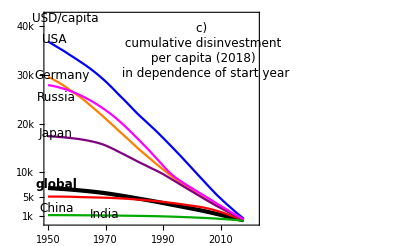

```mathematica
(*Fig2c=ListLinePlot[{percapdata[[2;;,{1,22}]],percapdata[[2;;,{1,2}]],percapdata[[2;;,{1,3}]],percapdata[[2;;,{1,5}]],percapdata[[2;;,{1,6}]],percapdata[[2;;,{1,7}]],percapdata[[2;;,{1,4}]]},PlotStyle->{{Black,AbsoluteThickness[3]}, Blue, Red,Orange,Purple,Darker[Green],Magenta},IntervalMarkers->"None",PlotRange->{{1950,2022},{0,42000}},Frame->{True,True,False,False},FrameTicks->{{{{1000,"1k"},{5000,"5k"},{10000,"10k"},{20000,"20k"},{30000,"30k"},{40000,"40k"}},None},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Automatic},Epilog->{Text[Style["Russia",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.06,0.6}]],{0,0}],Text[Style["USD/capita",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.1,0.97}]],{0,0}],Text[Style["c) \n cumulative disinvestment \n per capita (2018) \n in dependence of start year",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.74,0.82}]],{0,0}],Text[Style["USA",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.05,0.87}]],{0,0}],Text[Style["China",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.06,0.08}]],{0,0}],
Text[Style["India",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.28,0.05}]],{0,0}],
Text[Style["Japan",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.055,0.43}]],{0,0}],
Text[Style["Germany",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.085,0.705}]],{0,0}],
Text[Style["global",{FontFamily->"Helvetica",FontSize->12,Bold}],Offset[{0,0},Scaled[{0.06,0.19}]],{0,0}]},ImageSize->8.7*72/2.54*{GoldenRatio,1}]*)
```

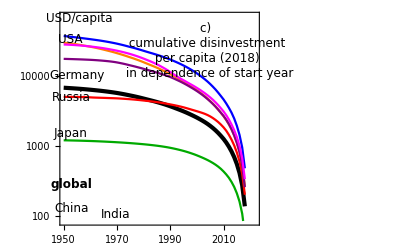

```mathematica
(*Fig2calt=ListLogPlot[{percapdata[[2;;,{1,22}]],percapdata[[2;;,{1,2}]],percapdata[[2;;,{1,3}]],percapdata[[2;;,{1,5}]],percapdata[[2;;,{1,6}]],percapdata[[2;;,{1,7}]],percapdata[[2;;,{1,4}]]},Joined->True,PlotStyle->{{Black,AbsoluteThickness[3]}, Blue, Red,Orange,Purple,Darker[Green],Magenta},IntervalMarkers->"None",PlotRange->{{1950,2022},{0,70000}},Frame->{True,True,False,False},FrameTicks->{{{{1000,"1k"},{5000,"5k"},{10000,"10k"},{20000,"20k"},{30000,"30k"},{40000,"40k"}},None},{{1950,1960,1970,1980,1990,2000,2010,2018},None}},FrameStyle->{Black,Black,Automatic,Automatic},Epilog->{Text[Style["Russia",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.06,0.6}]],{0,0}],Text[Style["USD/capita",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.1,0.97}]],{0,0}],Text[Style["c) \n cumulative disinvestment \n per capita (2018) \n in dependence of start year",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.74,0.82}]],{0,0}],Text[Style["USA",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.05,0.87}]],{0,0}],Text[Style["China",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.06,0.08}]],{0,0}],
Text[Style["India",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.28,0.05}]],{0,0}],
Text[Style["Japan",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.055,0.43}]],{0,0}],
Text[Style["Germany",{FontFamily->"Helvetica",FontSize->12}],Offset[{0,0},Scaled[{0.085,0.705}]],{0,0}],
Text[Style["global",{FontFamily->"Helvetica",FontSize->12,Bold}],Offset[{0,0},Scaled[{0.06,0.19}]],{0,0}]},ImageSize->8.7*72/2.54*{GoldenRatio,1}]*)
```

```mathematica
(*Fig2=Grid[{{Fig2a},{Fig2b},{Fig2c}}]*)
(*Fig2=Grid[{{Fig2a},{Fig2b}}]*)
(*Fig2b=Grid[{{Fig2a},{Fig2bc}}]*)
```

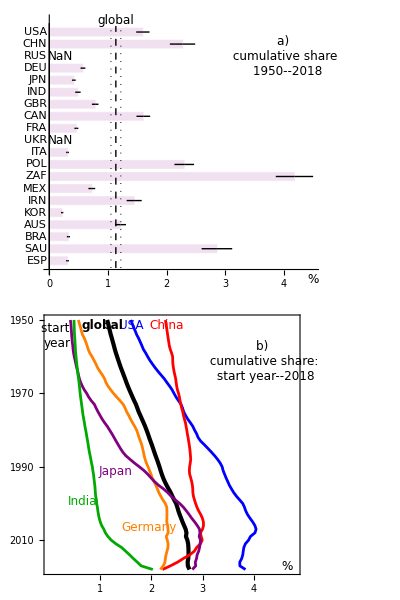

```mathematica
Fig2=Grid[{{Fig2a},{Fig2bc}}]
```

```mathematica
SetDirectory["C:\\Users\\Rickels\\Dropbox\\Historic_DICE_Dropbox\\Figures"];
```

```mathematica
Export["Figure2.eps",Fig2]
Export["Figure2.pdf",Fig2]
```

Figure2.eps

Figure2.pdf

```mathematica
SetDirectory["C:\\Users\\Rickels\\Dropbox\\Historic_DICE_Dropbox\\IW_calculations\\Country_Results"];
```

```mathematica
wdata=Import["disinvestment_data.csv"];
wplot=Table[0,{i,218},{j,6}];
wplot[[1]]={"country","ISO","MtC","GtC","bnUSD_RMQ","bnUSD_Drupp"};
wplot[[2;;,1;;4]]=wdata[[3;;,1;;4]];
Do[wplot[[i,5]]=Around[wdata[[i+1,7]]/1000,wdata[[i+1,8]]/1000],{i,2,218}]
Do[wplot[[i,6]]=Around[wdata[[i+1,11]]/1000,wdata[[i+1,12]]/1000],{i,2,218}]
```

```mathematica
wplot[[1;;6]]//MatrixForm
```

(country | ISO | MtC | GtC | bnUSD_RMQ | bnUSD_Drupp
USA | USA | 86100.8 | 86.1008 | 12.10.9 | 18.31.3
China | CHN | 56774.7 | 56.7747 | 7.20.7 | 11.71.1
Russian Federation | RUS | 28795.6 | 28.7956 | 4.070.30 | 6.10.4
Germany | DEU | 17085.1 | 17.0851 | 2.460.18 | 3.660.25
Japan | JPN | 16229.3 | 16.2293 | 2.220.17 | 3.430.26)

```mathematica
wregress=Table[0,{i,215},{j,11}];
wregress[[1;;163]]=wdata[[2;;164]];
wregress[[164;;179]]=wdata[[166;;181]];
wregress[[180;;210]]=wdata[[183;;213]];
wregress[[211;;]]=wdata[[215;;]];
wregress[[2;;,5;;]]=wregress[[2;;,5;;]]/1000;
(*lwregress=wregress;
lwregress[[2;;,3;;]]=Log[wregress[[2;;,3;;]]];*)
fitRMQ=LinearModelFit[wregress[[2;;,{4,7}]],x,x]
fitRMQ[{"RSquared","ParameterTable"}]
fitDrupp=LinearModelFit[wregress[[2;;,{4,11}]],x,x]
fitDrupp[{"RSquared","ParameterTable"}]
```

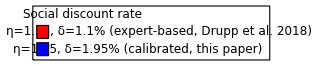

```mathematica
l3=Show[Graphics[{EdgeForm[Directive[Black,Thin]],White,Rectangle[{0,0},{12,2.5}]},ImageSize->320],Graphics[Text[Style["Social discount rate",{FontFamily->"Helvetica",FontSize->12},LineSpacing->{0,12}],{2.5,2.1}]],Graphics[{EdgeForm[Directive[Black,Thin]],Red,Rectangle[{0.2,1},{0.8,1.6}]}],Graphics[{EdgeForm[Directive[Black,Thin]],Blue,Rectangle[{0.2,0.2},{0.8,0.8}]}],Graphics[Text[Style["η=1.35, δ=1.1% (expert-based, Drupp et al. 2018)",{FontFamily->"Helvetica",FontSize->12},LineSpacing->{0,14}],{6.4,1.3}]],Graphics[Text[Style["η=1.45, δ=1.95% (calibrated, this paper)",{FontFamily->"Helvetica",FontSize->12},LineSpacing->{0,14}],{5.3,0.5}]]]
```

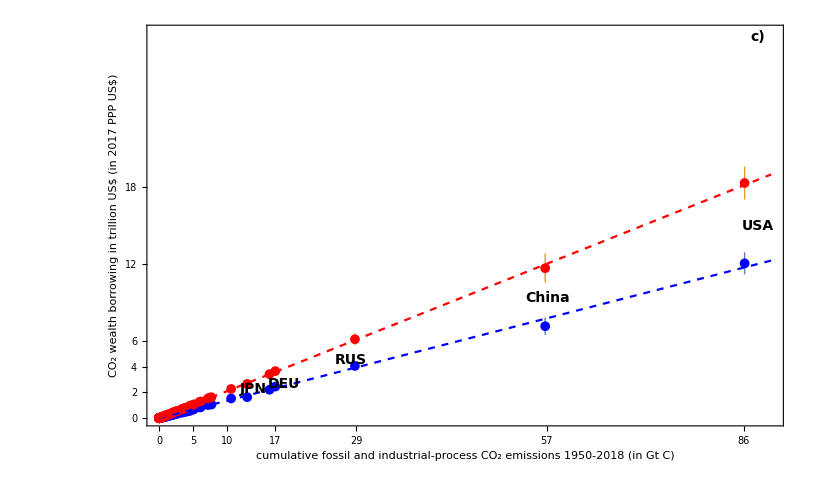

```mathematica
Fig3=Show[ListPlot[{wplot[[2;;,{4,5}]],wplot[[2;;,{4,6}]]},PlotStyle->{{Blue,AbsolutePointSize[7]},{Red,AbsolutePointSize[7]}},IntervalMarkers->"Fences",Axes->False,Frame->{True,True,False,False},PlotRange->{{0,90},{0,30}},FrameTicks->{{{0,2,4,6,12,18},None},{{0,5,10,17,29,57,86},None}},FrameStyle->{Black,Black,Automatic,Black},FrameLabel->{"cumulative fossil and industrial-process CO_2 emissions 1950-2018 (in Gt C)","CO_2 wealth borrowing in trillion US$ (in 2017 PPP US$)",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],Epilog->{Text[Style["c)",{FontFamily->"Helvetica",FontSize->14,Bold}],Offset[{0,0},Scaled[{0.96,0.97}]],{0,0}],Text[Style["USA",{FontFamily->"Helvetica",FontSize->14,Bold}],Offset[{0,0},Scaled[{0.96,0.5}]],{0,0}],Text[Style["China",{FontFamily->"Helvetica",FontSize->14,Bold}],Offset[{0,0},Scaled[{0.63,0.32}]],{0,0}],Text[Style["RUS",{FontFamily->"Helvetica",FontSize->14,Bold}],Offset[{0,0},Scaled[{0.32,0.165}]],{0,0}],Text[Style["DEU",{FontFamily->"Helvetica",FontSize->14,Bold}],Offset[{0,0},Scaled[{0.215,0.105}]],{0,0}],Text[Style["JPN",{FontFamily->"Helvetica",FontSize->14,Bold}],Offset[{0,0},Scaled[{0.168,0.0915}]],{0,0}],Inset[Figure1new,{22,23.8},Automatic,Scaled[0.45]],Inset[Figure2newb,{62,23.8},Automatic,Scaled[0.43]],Inset[l3,{70,3},Automatic,Scaled[0.43]]},ImageSize->17.8*72/2.54*{GoldenRatio,1}],Plot[fitRMQ[x],{x,0,90},PlotStyle->{Dashed,Blue}],Plot[fitDrupp[x],{x,0,90},PlotStyle->{Dashed,Red},Axes->False]]
```

```mathematica
Export["fig_disinvestment.pdf",Fig3]
Export["fig1_disinvestment.eps",Fig3]
```

fig_disinvestment.pdf

fig1_disinvestment.eps

```mathematica
(*Fig3L=Show[ListLogLogPlot[{wplot[[2;;100,{3,4}]],wplot[[2;;100,{3,5}]]},PlotStyle->{Blue,Red},PlotRange->Full,IntervalMarkers->"Fences",ImageSize->17.8*72/2.54*{GoldenRatio,1}],Plot[lfitRMQ[x],{x,4.7,90},PlotStyle->{Blue, Dashed}],Plot[lfitDrupp[x],{x,4.7,90},PlotStyle->{Red, Dashed}]]*)
```

```mathematica
Export["fig3L.pdf",Fig3L]
```

fig3L.pdf

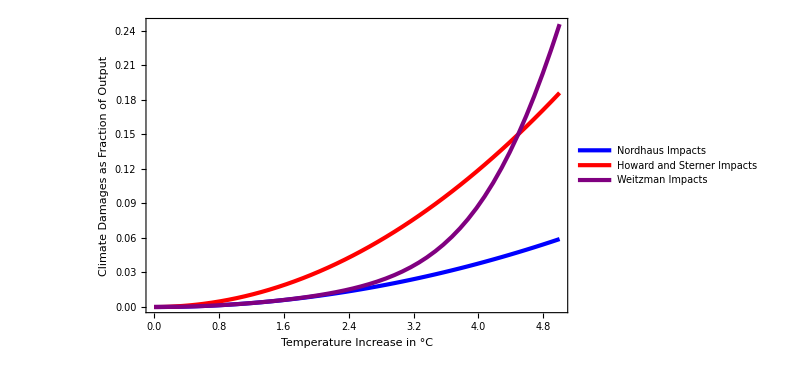

```mathematica
SIFigImpacts=Legended[Plot[{CImN[x],CImS[x],CImW[x]},{x,0,5},PlotStyle->{{Blue,AbsoluteThickness[3]},{Red,AbsoluteThickness[3]},{Purple,AbsoluteThickness[3]}},Frame->{True,True,False,False},FrameLabel->{"Temperature Increase in °C","Climate Damages as Fraction of Output",None,None},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],ImageSize->600],Placed[LineLegend[{{Blue,AbsoluteThickness[3]},{Red,AbsoluteThickness[3]},{Purple,AbsoluteThickness[3]}
,Black},{Style["Nordhaus Impacts",FontFamily->"Helvetica",FontSize->14],Style["Howard and Sterner Impacts",FontFamily->"Helvetica",FontSize->14],Style["Weitzman Impacts",FontFamily->"Helvetica",FontSize->14]},LegendLayout->{"Row",3}],Below]]
```

```mathematica
Export["SI_ClimateImpacts.eps",SIFigImpacts]
```

SI_ClimateImpacts.eps

```mathematica
abatdat=Import["historic_mu.csv"];
```

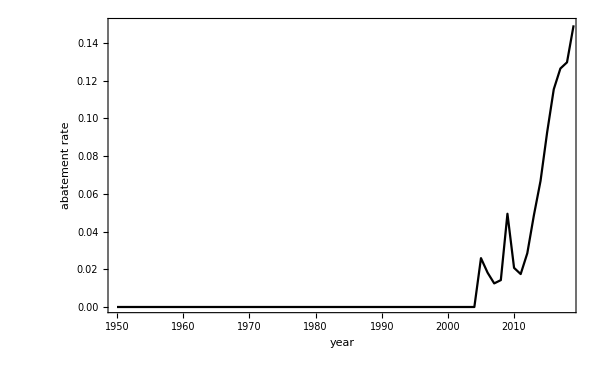

```mathematica
Fhismu=ListLinePlot[abatdat[[2;;,{1,2}]],PlotStyle->Black,PlotRange->{{1950,2018},{0,0.15}},Frame->{True,True,False,False},FrameLabel->{"year","abatement rate",None,None},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],ImageSize->600]
```

```mathematica
Export["Fhismu.eps",Fhismu]
```

Fhismu.eps